```mathematica
embedding = ExternalEvaluate["Python", "import torch;torch.load('/Users/ChengLuhan/eval_output/embedding.pth', map_location=torch.device('cpu')).numpy()"]
(*spec=Import["/Users/ChengLuhan/eval_output/spec.csv"];*)
spev = Import["/Users/ChengLuhan/Downloads/data_output.csv"]
```

NumericArray[…]

{{url,moa,x.pca,y.pca,x.tsne,y.tsne,x.umap,y.umap},{Week1_22123_Week1_150607_B02_montaged.jpeg,DMSO,-0.0126444,-0.00671056,8.13627,-26.084,14.8224,-6.7428},740,{Week9_39301_Week9_090907_G02_montaged.jpeg,Microtubule stabilizers,-0.0120702,-0.00439085,-25.3436,-37.087,22.0711,-0.820628},{Week9_39301_Week9_090907_G11_montaged.jpeg,DMSO,-0.0143111,-0.00426547,-24.663,-36.481,22.0751,-0.818325}}
 |  |  |  |

```mathematica
plot2d = FeatureSpacePlot[Normal[embedding]-> spec["moa"]];
```

```mathematica
plot3d =FeatureSpacePlot3D[Normal[embedding]-> spec["moa"], ImageSize->Large];
```

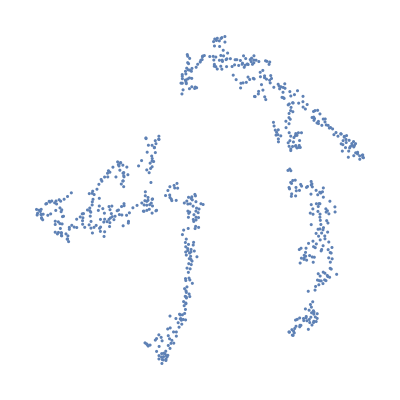

```mathematica
plot2d
```

```mathematica
spec = Import ["/Users/ChengLuhan/Downloads/data_output.csv"]
spec = AssociationThread[spec[[1]],spec[[2;;-1]]//Transpose]
```

{{url,moa,x.pca,y.pca,x.tsne,y.tsne,x.umap,y.umap},{Week1_22123_Week1_150607_B02_montaged.jpeg,DMSO,-0.0126444,-0.00671056,8.13627,-26.084,14.8224,-6.7428},740,{Week9_39301_Week9_090907_G02_montaged.jpeg,Microtubule stabilizers,-0.0120702,-0.00439085,-25.3436,-37.087,22.0711,-0.820628},{Week9_39301_Week9_090907_G11_montaged.jpeg,DMSO,-0.0143111,-0.00426547,-24.663,-36.481,22.0751,-0.818325}}
 |  |  |  |

<|url→{Week1_22123_Week1_150607_B02_montaged.jpeg,Week1_22123_Week1_150607_B03_montaged.jpeg,Week1_22123_Week1_150607_B04_montaged.jpeg,Week1_22123_Week1_150607_B11_montaged.jpeg,Week1_22123_Week1_150607_C02_montaged.jpeg,Week1_22123_Week1_150607_C11_montaged.jpeg,Week1_22123_Week1_150607_D02_montaged.jpeg,Week1_22123_Week1_150607_D03_montaged.jpeg,Week1_22123_Week1_150607_D04_montaged.jpeg,Week1_22123_Week1_150607_D05_montaged.jpeg,Week1_22123_Week1_150607_D11_montaged.jpeg,Week1_22123_Week1_150607_E02_montaged.jpeg,Week1_22123_Week1_150607_E03_montaged.jpeg,Week1_22123_Week1_150607_E04_montaged.jpeg,Week1_22123_Week1_150607_E11_montaged.jpeg,Week1_22123_Week1_150607_F02_montaged.jpeg,Week1_22123_Week1_150607_F11_montaged.jpeg,Week1_22123_Week1_150607_G02_montaged.jpeg,Week1_22123_Week1_150607_G03_montaged.jpeg,Week1_22123_Week1_150607_G04_montaged.jpeg,Week1_22123_Week1_150607_G05_montaged.jpeg,Week1_22123_Week1_150607_G06_montaged.jpeg,Week1_22123_Week1_150607_G07_montaged.jpeg,Week1_22123_Week1_150607_G08_montaged.jpeg,Week1_22123_Week1_150607_G11_montaged.jpeg,Week1_22141_Week1_150607_B02_montaged.jpeg,Week1_22141_Week1_150607_B03_montaged.jpeg,Week1_22141_Week1_150607_B04_montaged.jpeg,Week1_22141_Week1_150607_B11_montaged.jpeg,Week1_22141_Week1_150607_C02_montaged.jpeg,Week1_22141_Week1_150607_C11_montaged.jpeg,Week1_22141_Week1_150607_D02_montaged.jpeg,Week1_22141_Week1_150607_D03_montaged.jpeg,Week1_22141_Week1_150607_D04_montaged.jpeg,Week1_22141_Week1_150607_D05_montaged.jpeg,Week1_22141_Week1_150607_D11_montaged.jpeg,Week1_22141_Week1_150607_E02_montaged.jpeg,Week1_22141_Week1_150607_E03_montaged.jpeg,Week1_22141_Week1_150607_E04_montaged.jpeg,Week1_22141_Week1_150607_E11_montaged.jpeg,Week1_22141_Week1_150607_F02_montaged.jpeg,Week1_22141_Week1_150607_F11_montaged.jpeg,Week1_22141_Week1_150607_G02_montaged.jpeg,Week1_22141_Week1_150607_G03_montaged.jpeg,Week1_22141_Week1_150607_G04_montaged.jpeg,Week1_22141_Week1_150607_G05_montaged.jpeg,Week1_22141_Week1_150607_G06_montaged.jpeg,Week1_22141_Week1_150607_G07_montaged.jpeg,Week1_22141_Week1_150607_G08_montaged.jpeg,Week1_22141_Week1_150607_G11_montaged.jpeg,Week1_22161_Week1_150607_B02_montaged.jpeg,Week1_22161_Week1_150607_B03_montaged.jpeg,Week1_22161_Week1_150607_B04_montaged.jpeg,Week1_22161_Week1_150607_B11_montaged.jpeg,Week1_22161_Week1_150607_C02_montaged.jpeg,Week1_22161_Week1_150607_C11_montaged.jpeg,Week1_22161_Week1_150607_D02_montaged.jpeg,Week1_22161_Week1_150607_D03_montaged.jpeg,Week1_22161_Week1_150607_D04_montaged.jpeg,Week1_22161_Week1_150607_D05_montaged.jpeg,Week1_22161_Week1_150607_D11_montaged.jpeg,Week1_22161_Week1_150607_E02_montaged.jpeg,Week1_22161_Week1_150607_E03_montaged.jpeg,Week1_22161_Week1_150607_E04_montaged.jpeg,Week1_22161_Week1_150607_E11_montaged.jpeg,Week1_22161_Week1_150607_F02_montaged.jpeg,Week1_22161_Week1_150607_F11_montaged.jpeg,Week1_22161_Week1_150607_G02_montaged.jpeg,Week1_22161_Week1_150607_G03_montaged.jpeg,Week1_22161_Week1_150607_G04_montaged.jpeg,Week1_22161_Week1_150607_G05_montaged.jpeg,Week1_22161_Week1_150607_G06_montaged.jpeg,Week1_22161_Week1_150607_G07_montaged.jpeg,Week1_22161_Week1_150607_G08_montaged.jpeg,Week1_22161_Week1_150607_G11_montaged.jpeg,Week1_22361_Week1_150607_B02_montaged.jpeg,Week1_22361_Week1_150607_B05_montaged.jpeg,Week1_22361_Week1_150607_B06_montaged.jpeg,Week1_22361_Week1_150607_B11_montaged.jpeg,Week1_22361_Week1_150607_C02_montaged.jpeg,Week1_22361_Week1_150607_C11_montaged.jpeg,Week1_22361_Week1_150607_D02_montaged.jpeg,Week1_22361_Week1_150607_D04_montaged.jpeg,Week1_22361_Week1_150607_D05_montaged.jpeg,Week1_22361_Week1_150607_D06_montaged.jpeg,Week1_22361_Week1_150607_D11_montaged.jpeg,Week1_22361_Week1_150607_E02_montaged.jpeg,Week1_22361_Week1_150607_E07_montaged.jpeg,Week1_22361_Week1_150607_E11_montaged.jpeg,Week1_22361_Week1_150607_F02_montaged.jpeg,Week1_22361_Week1_150607_F11_montaged.jpeg,Week1_22361_Week1_150607_G02_montaged.jpeg,Week1_22361_Week1_150607_G11_montaged.jpeg,Week1_22381_Week1_150607_B02_montaged.jpeg,Week1_22381_Week1_150607_B05_montaged.jpeg,Week1_22381_Week1_150607_B06_montaged.jpeg,Week1_22381_Week1_150607_B11_montaged.jpeg,Week1_22381_Week1_150607_C02_montaged.jpeg,Week1_22381_Week1_150607_C11_montaged.jpeg,Week1_22381_Week1_150607_D02_montaged.jpeg,Week1_22381_Week1_150607_D04_montaged.jpeg,Week1_22381_Week1_150607_D05_montaged.jpeg,Week1_22381_Week1_150607_D06_montaged.jpeg,Week1_22381_Week1_150607_D11_montaged.jpeg,Week1_22381_Week1_150607_E02_montaged.jpeg,Week1_22381_Week1_150607_E07_montaged.jpeg,Week1_22381_Week1_150607_E11_montaged.jpeg,Week1_22381_Week1_150607_F02_montaged.jpeg,Week1_22381_Week1_150607_F11_montaged.jpeg,Week1_22381_Week1_150607_G02_montaged.jpeg,Week1_22381_Week1_150607_G11_montaged.jpeg,Week1_22401_Week1_150607_B02_montaged.jpeg,Week1_22401_Week1_150607_B05_montaged.jpeg,Week1_22401_Week1_150607_B06_montaged.jpeg,Week1_22401_Week1_150607_B11_montaged.jpeg,Week1_22401_Week1_150607_C02_montaged.jpeg,Week1_22401_Week1_150607_C11_montaged.jpeg,Week1_22401_Week1_150607_D02_montaged.jpeg,Week1_22401_Week1_150607_D04_montaged.jpeg,Week1_22401_Week1_150607_D05_montaged.jpeg,Week1_22401_Week1_150607_D06_montaged.jpeg,Week1_22401_Week1_150607_D11_montaged.jpeg,Week1_22401_Week1_150607_E02_montaged.jpeg,Week1_22401_Week1_150607_E07_montaged.jpeg,Week1_22401_Week1_150607_E11_montaged.jpeg,Week1_22401_Week1_150607_F02_montaged.jpeg,Week1_22401_Week1_150607_F11_montaged.jpeg,Week1_22401_Week1_150607_G02_montaged.jpeg,Week1_22401_Week1_150607_G11_montaged.jpeg,Week2_24121_Week2_180607_B02_montaged.jpeg,Week2_24121_Week2_180607_B06_montaged.jpeg,Week2_24121_Week2_180607_B11_montaged.jpeg,Week2_24121_Week2_180607_C02_montaged.jpeg,Week2_24121_Week2_180607_C11_montaged.jpeg,Week2_24121_Week2_180607_D02_montaged.jpeg,Week2_24121_Week2_180607_D03_montaged.jpeg,Week2_24121_Week2_180607_D06_montaged.jpeg,Week2_24121_Week2_180607_D11_montaged.jpeg,Week2_24121_Week2_180607_E02_montaged.jpeg,Week2_24121_Week2_180607_E11_montaged.jpeg,Week2_24121_Week2_180607_F02_montaged.jpeg,Week2_24121_Week2_180607_F11_montaged.jpeg,Week2_24121_Week2_180607_G02_montaged.jpeg,Week2_24121_Week2_180607_G03_montaged.jpeg,Week2_24121_Week2_180607_G11_montaged.jpeg,Week2_24141_Week2_180607_B02_montaged.jpeg,Week2_24141_Week2_180607_B06_montaged.jpeg,Week2_24141_Week2_180607_B11_montaged.jpeg,Week2_24141_Week2_180607_C02_montaged.jpeg,Week2_24141_Week2_180607_C11_montaged.jpeg,Week2_24141_Week2_180607_D02_montaged.jpeg,Week2_24141_Week2_180607_D03_montaged.jpeg,Week2_24141_Week2_180607_D06_montaged.jpeg,Week2_24141_Week2_180607_D11_montaged.jpeg,Week2_24141_Week2_180607_E02_montaged.jpeg,Week2_24141_Week2_180607_E11_montaged.jpeg,Week2_24141_Week2_180607_F02_montaged.jpeg,Week2_24141_Week2_180607_F11_montaged.jpeg,Week2_24141_Week2_180607_G02_montaged.jpeg,Week2_24141_Week2_180607_G03_montaged.jpeg,Week2_24141_Week2_180607_G11_montaged.jpeg,Week2_24161_Week2_180607_B02_montaged.jpeg,Week2_24161_Week2_180607_B06_montaged.jpeg,Week2_24161_Week2_180607_B11_montaged.jpeg,Week2_24161_Week2_180607_C02_montaged.jpeg,Week2_24161_Week2_180607_C11_montaged.jpeg,Week2_24161_Week2_180607_D02_montaged.jpeg,Week2_24161_Week2_180607_D03_montaged.jpeg,Week2_24161_Week2_180607_D06_montaged.jpeg,Week2_24161_Week2_180607_D11_montaged.jpeg,Week2_24161_Week2_180607_E02_montaged.jpeg,Week2_24161_Week2_180607_E11_montaged.jpeg,Week2_24161_Week2_180607_F02_montaged.jpeg,Week2_24161_Week2_180607_F11_montaged.jpeg,Week2_24161_Week2_180607_G02_montaged.jpeg,Week2_24161_Week2_180607_G03_montaged.jpeg,Week2_24161_Week2_180607_G11_montaged.jpeg,Week2_24361_Week2_180607_B02_montaged.jpeg,Week2_24361_Week2_180607_B11_montaged.jpeg,Week2_24361_Week2_180607_C02_montaged.jpeg,Week2_24361_Week2_180607_C06_montaged.jpeg,Week2_24361_Week2_180607_C09_montaged.jpeg,Week2_24361_Week2_180607_C11_montaged.jpeg,Week2_24361_Week2_180607_D02_montaged.jpeg,Week2_24361_Week2_180607_D11_montaged.jpeg,Week2_24361_Week2_180607_E02_montaged.jpeg,Week2_24361_Week2_180607_E11_montaged.jpeg,Week2_24361_Week2_180607_F02_montaged.jpeg,Week2_24361_Week2_180607_F11_montaged.jpeg,Week2_24361_Week2_180607_G02_montaged.jpeg,Week2_24361_Week2_180607_G11_montaged.jpeg,Week2_24381_Week2_180607_B02_montaged.jpeg,Week2_24381_Week2_180607_B11_montaged.jpeg,Week2_24381_Week2_180607_C02_montaged.jpeg,Week2_24381_Week2_180607_C06_montaged.jpeg,Week2_24381_Week2_180607_C09_montaged.jpeg,Week2_24381_Week2_180607_C11_montaged.jpeg,Week2_24381_Week2_180607_D02_montaged.jpeg,Week2_24381_Week2_180607_D11_montaged.jpeg,Week2_24381_Week2_180607_E02_montaged.jpeg,Week2_24381_Week2_180607_E11_montaged.jpeg,Week2_24381_Week2_180607_F02_montaged.jpeg,Week2_24381_Week2_180607_F11_montaged.jpeg,Week2_24381_Week2_180607_G02_montaged.jpeg,Week2_24381_Week2_180607_G11_montaged.jpeg,Week2_24401_Week2_180607_B02_montaged.jpeg,Week2_24401_Week2_180607_B11_montaged.jpeg,Week2_24401_Week2_180607_C02_montaged.jpeg,Week2_24401_Week2_180607_C06_montaged.jpeg,Week2_24401_Week2_180607_C09_montaged.jpeg,Week2_24401_Week2_180607_C11_montaged.jpeg,Week2_24401_Week2_180607_D02_montaged.jpeg,Week2_24401_Week2_180607_D11_montaged.jpeg,Week2_24401_Week2_180607_E02_montaged.jpeg,Week2_24401_Week2_180607_E11_montaged.jpeg,Week2_24401_Week2_180607_F02_montaged.jpeg,Week2_24401_Week2_180607_F11_montaged.jpeg,Week2_24401_Week2_180607_G02_montaged.jpeg,Week2_24401_Week2_180607_G11_montaged.jpeg,Week3_25421_Week3_290607_B02_montaged.jpeg,Week3_25421_Week3_290607_B04_montaged.jpeg,Week3_25421_Week3_290607_B05_montaged.jpeg,Week3_25421_Week3_290607_B06_montaged.jpeg,Week3_25421_Week3_290607_B07_montaged.jpeg,Week3_25421_Week3_290607_B08_montaged.jpeg,Week3_25421_Week3_290607_B09_montaged.jpeg,Week3_25421_Week3_290607_B10_montaged.jpeg,Week3_25421_Week3_290607_B11_montaged.jpeg,Week3_25421_Week3_290607_C02_montaged.jpeg,Week3_25421_Week3_290607_C11_montaged.jpeg,Week3_25421_Week3_290607_D02_montaged.jpeg,Week3_25421_Week3_290607_D03_montaged.jpeg,Week3_25421_Week3_290607_D04_montaged.jpeg,Week3_25421_Week3_290607_D05_montaged.jpeg,Week3_25421_Week3_290607_D06_montaged.jpeg,Week3_25421_Week3_290607_D07_montaged.jpeg,Week3_25421_Week3_290607_D08_montaged.jpeg,Week3_25421_Week3_290607_D09_montaged.jpeg,Week3_25421_Week3_290607_D11_montaged.jpeg,Week3_25421_Week3_290607_E02_montaged.jpeg,Week3_25421_Week3_290607_E06_montaged.jpeg,Week3_25421_Week3_290607_E07_montaged.jpeg,Week3_25421_Week3_290607_E08_montaged.jpeg,Week3_25421_Week3_290607_E11_montaged.jpeg,Week3_25421_Week3_290607_F02_montaged.jpeg,Week3_25421_Week3_290607_F04_montaged.jpeg,Week3_25421_Week3_290607_F05_montaged.jpeg,Week3_25421_Week3_290607_F06_montaged.jpeg,Week3_25421_Week3_290607_F11_montaged.jpeg,Week3_25421_Week3_290607_G02_montaged.jpeg,Week3_25421_Week3_290607_G11_montaged.jpeg,Week3_25441_Week3_290607_B02_montaged.jpeg,Week3_25441_Week3_290607_B04_montaged.jpeg,Week3_25441_Week3_290607_B05_montaged.jpeg,Week3_25441_Week3_290607_B06_montaged.jpeg,Week3_25441_Week3_290607_B07_montaged.jpeg,Week3_25441_Week3_290607_B08_montaged.jpeg,Week3_25441_Week3_290607_B09_montaged.jpeg,Week3_25441_Week3_290607_B10_montaged.jpeg,Week3_25441_Week3_290607_B11_montaged.jpeg,Week3_25441_Week3_290607_C02_montaged.jpeg,Week3_25441_Week3_290607_C11_montaged.jpeg,Week3_25441_Week3_290607_D02_montaged.jpeg,Week3_25441_Week3_290607_D03_montaged.jpeg,Week3_25441_Week3_290607_D04_montaged.jpeg,Week3_25441_Week3_290607_D05_montaged.jpeg,Week3_25441_Week3_290607_D06_montaged.jpeg,Week3_25441_Week3_290607_D07_montaged.jpeg,Week3_25441_Week3_290607_D08_montaged.jpeg,Week3_25441_Week3_290607_D09_montaged.jpeg,Week3_25441_Week3_290607_D11_montaged.jpeg,Week3_25441_Week3_290607_E02_montaged.jpeg,Week3_25441_Week3_290607_E06_montaged.jpeg,Week3_25441_Week3_290607_E07_montaged.jpeg,Week3_25441_Week3_290607_E08_montaged.jpeg,Week3_25441_Week3_290607_E11_montaged.jpeg,Week3_25441_Week3_290607_F02_montaged.jpeg,Week3_25441_Week3_290607_F04_montaged.jpeg,Week3_25441_Week3_290607_F05_montaged.jpeg,Week3_25441_Week3_290607_F06_montaged.jpeg,Week3_25441_Week3_290607_F11_montaged.jpeg,Week3_25441_Week3_290607_G02_montaged.jpeg,Week3_25441_Week3_290607_G11_montaged.jpeg,Week3_25461_Week3_290607_B02_montaged.jpeg,Week3_25461_Week3_290607_B04_montaged.jpeg,Week3_25461_Week3_290607_B05_montaged.jpeg,Week3_25461_Week3_290607_B06_montaged.jpeg,Week3_25461_Week3_290607_B07_montaged.jpeg,Week3_25461_Week3_290607_B08_montaged.jpeg,Week3_25461_Week3_290607_B09_montaged.jpeg,Week3_25461_Week3_290607_B10_montaged.jpeg,Week3_25461_Week3_290607_B11_montaged.jpeg,Week3_25461_Week3_290607_C02_montaged.jpeg,Week3_25461_Week3_290607_C11_montaged.jpeg,Week3_25461_Week3_290607_D02_montaged.jpeg,Week3_25461_Week3_290607_D03_montaged.jpeg,Week3_25461_Week3_290607_D04_montaged.jpeg,Week3_25461_Week3_290607_D05_montaged.jpeg,Week3_25461_Week3_290607_D06_montaged.jpeg,Week3_25461_Week3_290607_D07_montaged.jpeg,Week3_25461_Week3_290607_D08_montaged.jpeg,Week3_25461_Week3_290607_D09_montaged.jpeg,Week3_25461_Week3_290607_D11_montaged.jpeg,Week3_25461_Week3_290607_E02_montaged.jpeg,Week3_25461_Week3_290607_E06_montaged.jpeg,Week3_25461_Week3_290607_E07_montaged.jpeg,Week3_25461_Week3_290607_E08_montaged.jpeg,Week3_25461_Week3_290607_E11_montaged.jpeg,Week3_25461_Week3_290607_F02_montaged.jpeg,Week3_25461_Week3_290607_F04_montaged.jpeg,Week3_25461_Week3_290607_F05_montaged.jpeg,Week3_25461_Week3_290607_F06_montaged.jpeg,Week3_25461_Week3_290607_F11_montaged.jpeg,Week3_25461_Week3_290607_G02_montaged.jpeg,Week3_25461_Week3_290607_G11_montaged.jpeg,Week3_25681_Week3_290607_B02_montaged.jpeg,Week3_25681_Week3_290607_B03_montaged.jpeg,Week3_25681_Week3_290607_B04_montaged.jpeg,Week3_25681_Week3_290607_B05_montaged.jpeg,Week3_25681_Week3_290607_B06_montaged.jpeg,Week3_25681_Week3_290607_B11_montaged.jpeg,Week3_25681_Week3_290607_C02_montaged.jpeg,Week3_25681_Week3_290607_C06_montaged.jpeg,Week3_25681_Week3_290607_C07_montaged.jpeg,Week3_25681_Week3_290607_C08_montaged.jpeg,Week3_25681_Week3_290607_C11_montaged.jpeg,Week3_25681_Week3_290607_D02_montaged.jpeg,Week3_25681_Week3_290607_D11_montaged.jpeg,Week3_25681_Week3_290607_E02_montaged.jpeg,Week3_25681_Week3_290607_E04_montaged.jpeg,Week3_25681_Week3_290607_E11_montaged.jpeg,Week3_25681_Week3_290607_F02_montaged.jpeg,Week3_25681_Week3_290607_F03_montaged.jpeg,Week3_25681_Week3_290607_F11_montaged.jpeg,Week3_25681_Week3_290607_G02_montaged.jpeg,Week3_25681_Week3_290607_G11_montaged.jpeg,Week3_25701_Week3_290607_B02_montaged.jpeg,Week3_25701_Week3_290607_B03_montaged.jpeg,Week3_25701_Week3_290607_B04_montaged.jpeg,Week3_25701_Week3_290607_B05_montaged.jpeg,Week3_25701_Week3_290607_B06_montaged.jpeg,Week3_25701_Week3_290607_B11_montaged.jpeg,Week3_25701_Week3_290607_C02_montaged.jpeg,Week3_25701_Week3_290607_C06_montaged.jpeg,Week3_25701_Week3_290607_C07_montaged.jpeg,Week3_25701_Week3_290607_C08_montaged.jpeg,Week3_25701_Week3_290607_C11_montaged.jpeg,Week3_25701_Week3_290607_D02_montaged.jpeg,Week3_25701_Week3_290607_D11_montaged.jpeg,Week3_25701_Week3_290607_E02_montaged.jpeg,Week3_25701_Week3_290607_E04_montaged.jpeg,Week3_25701_Week3_290607_E11_montaged.jpeg,Week3_25701_Week3_290607_F02_montaged.jpeg,Week3_25701_Week3_290607_F03_montaged.jpeg,Week3_25701_Week3_290607_F11_montaged.jpeg,Week3_25701_Week3_290607_G02_montaged.jpeg,Week3_25701_Week3_290607_G11_montaged.jpeg,Week3_25721_Week3_290607_B02_montaged.jpeg,Week3_25721_Week3_290607_B03_montaged.jpeg,Week3_25721_Week3_290607_B04_montaged.jpeg,Week3_25721_Week3_290607_B05_montaged.jpeg,Week3_25721_Week3_290607_B06_montaged.jpeg,Week3_25721_Week3_290607_B11_montaged.jpeg,Week3_25721_Week3_290607_C02_montaged.jpeg,Week3_25721_Week3_290607_C06_montaged.jpeg,Week3_25721_Week3_290607_C07_montaged.jpeg,Week3_25721_Week3_290607_C08_montaged.jpeg,Week3_25721_Week3_290607_C11_montaged.jpeg,Week3_25721_Week3_290607_D02_montaged.jpeg,Week3_25721_Week3_290607_D11_montaged.jpeg,Week3_25721_Week3_290607_E02_montaged.jpeg,Week3_25721_Week3_290607_E04_montaged.jpeg,Week3_25721_Week3_290607_E11_montaged.jpeg,Week3_25721_Week3_290607_F02_montaged.jpeg,Week3_25721_Week3_290607_F03_montaged.jpeg,Week3_25721_Week3_290607_F11_montaged.jpeg,Week3_25721_Week3_290607_G02_montaged.jpeg,Week3_25721_Week3_290607_G11_montaged.jpeg,Week5_28901_Week5_130707_B02_montaged.jpeg,Week5_28901_Week5_130707_B03_montaged.jpeg,Week5_28901_Week5_130707_B04_montaged.jpeg,Week5_28901_Week5_130707_B05_montaged.jpeg,Week5_28901_Week5_130707_B11_montaged.jpeg,Week5_28901_Week5_130707_C02_montaged.jpeg,Week5_28901_Week5_130707_C11_montaged.jpeg,Week5_28901_Week5_130707_D02_montaged.jpeg,Week5_28901_Week5_130707_D11_montaged.jpeg,Week5_28901_Week5_130707_E02_montaged.jpeg,Week5_28901_Week5_130707_E11_montaged.jpeg,Week5_28901_Week5_130707_F02_montaged.jpeg,Week5_28901_Week5_130707_F11_montaged.jpeg,Week5_28901_Week5_130707_G02_montaged.jpeg,Week5_28901_Week5_130707_G11_montaged.jpeg,Week5_28921_Week5_130707_B02_montaged.jpeg,Week5_28921_Week5_130707_B03_montaged.jpeg,Week5_28921_Week5_130707_B04_montaged.jpeg,Week5_28921_Week5_130707_B05_montaged.jpeg,Week5_28921_Week5_130707_B11_montaged.jpeg,Week5_28921_Week5_130707_C02_montaged.jpeg,Week5_28921_Week5_130707_C11_montaged.jpeg,Week5_28921_Week5_130707_D02_montaged.jpeg,Week5_28921_Week5_130707_D11_montaged.jpeg,Week5_28921_Week5_130707_E02_montaged.jpeg,Week5_28921_Week5_130707_E11_montaged.jpeg,Week5_28921_Week5_130707_F02_montaged.jpeg,Week5_28921_Week5_130707_F11_montaged.jpeg,Week5_28921_Week5_130707_G02_montaged.jpeg,Week5_28921_Week5_130707_G11_montaged.jpeg,Week5_28961_Week5_130707_B02_montaged.jpeg,Week5_28961_Week5_130707_B03_montaged.jpeg,Week5_28961_Week5_130707_B04_montaged.jpeg,Week5_28961_Week5_130707_B05_montaged.jpeg,Week5_28961_Week5_130707_B11_montaged.jpeg,Week5_28961_Week5_130707_C02_montaged.jpeg,Week5_28961_Week5_130707_C11_montaged.jpeg,Week5_28961_Week5_130707_D02_montaged.jpeg,Week5_28961_Week5_130707_D11_montaged.jpeg,Week5_28961_Week5_130707_E02_montaged.jpeg,Week5_28961_Week5_130707_E11_montaged.jpeg,Week5_28961_Week5_130707_F02_montaged.jpeg,Week5_28961_Week5_130707_F11_montaged.jpeg,Week5_28961_Week5_130707_G02_montaged.jpeg,Week5_28961_Week5_130707_G11_montaged.jpeg,Week5_29301_Week5_130707_B02_montaged.jpeg,Week5_29301_Week5_130707_B11_montaged.jpeg,Week5_29301_Week5_130707_C02_montaged.jpeg,Week5_29301_Week5_130707_C11_montaged.jpeg,Week5_29301_Week5_130707_D02_montaged.jpeg,Week5_29301_Week5_130707_D11_montaged.jpeg,Week5_29301_Week5_130707_E02_montaged.jpeg,Week5_29301_Week5_130707_E11_montaged.jpeg,Week5_29301_Week5_130707_F02_montaged.jpeg,Week5_29301_Week5_130707_F11_montaged.jpeg,Week5_29301_Week5_130707_G02_montaged.jpeg,Week5_29301_Week5_130707_G11_montaged.jpeg,Week5_29321_Week5_130707_B02_montaged.jpeg,Week5_29321_Week5_130707_B11_montaged.jpeg,Week5_29321_Week5_130707_C02_montaged.jpeg,Week5_29321_Week5_130707_C11_montaged.jpeg,Week5_29321_Week5_130707_D02_montaged.jpeg,Week5_29321_Week5_130707_D11_montaged.jpeg,Week5_29321_Week5_130707_E02_montaged.jpeg,Week5_29321_Week5_130707_E11_montaged.jpeg,Week5_29321_Week5_130707_F02_montaged.jpeg,Week5_29321_Week5_130707_F11_montaged.jpeg,Week5_29321_Week5_130707_G02_montaged.jpeg,Week5_29321_Week5_130707_G11_montaged.jpeg,Week5_29341_Week5_130707_B02_montaged.jpeg,Week5_29341_Week5_130707_B11_montaged.jpeg,Week5_29341_Week5_130707_C02_montaged.jpeg,Week5_29341_Week5_130707_C11_montaged.jpeg,Week5_29341_Week5_130707_D02_montaged.jpeg,Week5_29341_Week5_130707_D11_montaged.jpeg,Week5_29341_Week5_130707_E02_montaged.jpeg,Week5_29341_Week5_130707_E11_montaged.jpeg,Week5_29341_Week5_130707_F02_montaged.jpeg,Week5_29341_Week5_130707_F11_montaged.jpeg,Week5_29341_Week5_130707_G02_montaged.jpeg,Week5_29341_Week5_130707_G11_montaged.jpeg,Week6_31641_Week6_200607_B02_montaged.jpeg,Week6_31641_Week6_200607_B03_montaged.jpeg,Week6_31641_Week6_200607_B11_montaged.jpeg,Week6_31641_Week6_200607_C02_montaged.jpeg,Week6_31641_Week6_200607_C11_montaged.jpeg,Week6_31641_Week6_200607_D02_montaged.jpeg,Week6_31641_Week6_200607_D11_montaged.jpeg,Week6_31641_Week6_200607_E02_montaged.jpeg,Week6_31641_Week6_200607_E11_montaged.jpeg,Week6_31641_Week6_200607_F02_montaged.jpeg,Week6_31641_Week6_200607_F11_montaged.jpeg,Week6_31641_Week6_200607_G02_montaged.jpeg,Week6_31641_Week6_200607_G11_montaged.jpeg,Week6_31661_Week6_200607_B02_montaged.jpeg,Week6_31661_Week6_200607_B03_montaged.jpeg,Week6_31661_Week6_200607_B11_montaged.jpeg,Week6_31661_Week6_200607_C02_montaged.jpeg,Week6_31661_Week6_200607_C11_montaged.jpeg,Week6_31661_Week6_200607_D02_montaged.jpeg,Week6_31661_Week6_200607_D11_montaged.jpeg,Week6_31661_Week6_200607_E02_montaged.jpeg,Week6_31661_Week6_200607_E11_montaged.jpeg,Week6_31661_Week6_200607_F02_montaged.jpeg,Week6_31661_Week6_200607_F11_montaged.jpeg,Week6_31661_Week6_200607_G02_montaged.jpeg,Week6_31661_Week6_200607_G11_montaged.jpeg,Week6_31681_Week6_200607_B02_montaged.jpeg,Week6_31681_Week6_200607_B03_montaged.jpeg,Week6_31681_Week6_200607_B11_montaged.jpeg,Week6_31681_Week6_200607_C02_montaged.jpeg,Week6_31681_Week6_200607_C11_montaged.jpeg,Week6_31681_Week6_200607_D02_montaged.jpeg,Week6_31681_Week6_200607_D11_montaged.jpeg,Week6_31681_Week6_200607_E02_montaged.jpeg,Week6_31681_Week6_200607_E11_montaged.jpeg,Week6_31681_Week6_200607_F02_montaged.jpeg,Week6_31681_Week6_200607_F11_montaged.jpeg,Week6_31681_Week6_200607_G02_montaged.jpeg,Week6_31681_Week6_200607_G11_montaged.jpeg,Week6_32061_Week6_200607_B02_montaged.jpeg,Week6_32061_Week6_200607_B11_montaged.jpeg,Week6_32061_Week6_200607_C02_montaged.jpeg,Week6_32061_Week6_200607_C11_montaged.jpeg,Week6_32061_Week6_200607_D02_montaged.jpeg,Week6_32061_Week6_200607_D11_montaged.jpeg,Week6_32061_Week6_200607_E02_montaged.jpeg,Week6_32061_Week6_200607_E11_montaged.jpeg,Week6_32061_Week6_200607_F02_montaged.jpeg,Week6_32061_Week6_200607_F11_montaged.jpeg,Week6_32061_Week6_200607_G02_montaged.jpeg,Week6_32061_Week6_200607_G11_montaged.jpeg,Week6_32121_Week6_200607_B02_montaged.jpeg,Week6_32121_Week6_200607_B11_montaged.jpeg,Week6_32121_Week6_200607_C02_montaged.jpeg,Week6_32121_Week6_200607_C11_montaged.jpeg,Week6_32121_Week6_200607_D02_montaged.jpeg,Week6_32121_Week6_200607_D11_montaged.jpeg,Week6_32121_Week6_200607_E02_montaged.jpeg,Week6_32121_Week6_200607_E11_montaged.jpeg,Week6_32121_Week6_200607_F02_montaged.jpeg,Week6_32121_Week6_200607_F11_montaged.jpeg,Week6_32121_Week6_200607_G02_montaged.jpeg,Week6_32121_Week6_200607_G11_montaged.jpeg,Week6_32161_Week6_200607_B02_montaged.jpeg,Week6_32161_Week6_200607_B11_montaged.jpeg,Week6_32161_Week6_200607_C02_montaged.jpeg,Week6_32161_Week6_200607_C11_montaged.jpeg,Week6_32161_Week6_200607_D02_montaged.jpeg,Week6_32161_Week6_200607_D11_montaged.jpeg,Week6_32161_Week6_200607_E02_montaged.jpeg,Week6_32161_Week6_200607_E11_montaged.jpeg,Week6_32161_Week6_200607_F02_montaged.jpeg,Week6_32161_Week6_200607_F11_montaged.jpeg,Week6_32161_Week6_200607_G02_montaged.jpeg,Week6_32161_Week6_200607_G11_montaged.jpeg,Week7_34341_Week7_230707_B02_montaged.jpeg,Week7_34341_Week7_230707_B11_montaged.jpeg,Week7_34341_Week7_230707_C02_montaged.jpeg,Week7_34341_Week7_230707_C04_montaged.jpeg,Week7_34341_Week7_230707_C05_montaged.jpeg,Week7_34341_Week7_230707_C06_montaged.jpeg,Week7_34341_Week7_230707_C11_montaged.jpeg,Week7_34341_Week7_230707_D02_montaged.jpeg,Week7_34341_Week7_230707_D04_montaged.jpeg,Week7_34341_Week7_230707_D07_montaged.jpeg,Week7_34341_Week7_230707_D11_montaged.jpeg,Week7_34341_Week7_230707_E02_montaged.jpeg,Week7_34341_Week7_230707_E11_montaged.jpeg,Week7_34341_Week7_230707_F02_montaged.jpeg,Week7_34341_Week7_230707_F11_montaged.jpeg,Week7_34341_Week7_230707_G02_montaged.jpeg,Week7_34341_Week7_230707_G11_montaged.jpeg,Week7_34381_Week7_230707_B02_montaged.jpeg,Week7_34381_Week7_230707_B11_montaged.jpeg,Week7_34381_Week7_230707_C02_montaged.jpeg,Week7_34381_Week7_230707_C04_montaged.jpeg,Week7_34381_Week7_230707_C05_montaged.jpeg,Week7_34381_Week7_230707_C06_montaged.jpeg,Week7_34381_Week7_230707_C11_montaged.jpeg,Week7_34381_Week7_230707_D02_montaged.jpeg,Week7_34381_Week7_230707_D04_montaged.jpeg,Week7_34381_Week7_230707_D07_montaged.jpeg,Week7_34381_Week7_230707_D11_montaged.jpeg,Week7_34381_Week7_230707_E02_montaged.jpeg,Week7_34381_Week7_230707_E11_montaged.jpeg,Week7_34381_Week7_230707_F02_montaged.jpeg,Week7_34381_Week7_230707_F11_montaged.jpeg,Week7_34381_Week7_230707_G02_montaged.jpeg,Week7_34381_Week7_230707_G11_montaged.jpeg,Week8_38203_Week8_4sites_B02_montaged.jpeg,Week8_38203_Week8_4sites_B11_montaged.jpeg,Week8_38203_Week8_4sites_C02_montaged.jpeg,Week8_38203_Week8_4sites_C08_montaged.jpeg,Week8_38203_Week8_4sites_C09_montaged.jpeg,Week8_38203_Week8_4sites_C10_montaged.jpeg,Week8_38203_Week8_4sites_C11_montaged.jpeg,Week8_38203_Week8_4sites_D02_montaged.jpeg,Week8_38203_Week8_4sites_D11_montaged.jpeg,Week8_38203_Week8_4sites_E02_montaged.jpeg,Week8_38203_Week8_4sites_E11_montaged.jpeg,Week8_38203_Week8_4sites_F02_montaged.jpeg,Week8_38203_Week8_4sites_F11_montaged.jpeg,Week8_38203_Week8_4sites_G02_montaged.jpeg,Week8_38203_Week8_4sites_G11_montaged.jpeg,Week8_38221_Week8_4sites_B02_montaged.jpeg,Week8_38221_Week8_4sites_B11_montaged.jpeg,Week8_38221_Week8_4sites_C02_montaged.jpeg,Week8_38221_Week8_4sites_C08_montaged.jpeg,Week8_38221_Week8_4sites_C09_montaged.jpeg,Week8_38221_Week8_4sites_C10_montaged.jpeg,Week8_38221_Week8_4sites_C11_montaged.jpeg,Week8_38221_Week8_4sites_D02_montaged.jpeg,Week8_38221_Week8_4sites_D11_montaged.jpeg,Week8_38221_Week8_4sites_E02_montaged.jpeg,Week8_38221_Week8_4sites_E11_montaged.jpeg,Week8_38221_Week8_4sites_F02_montaged.jpeg,Week8_38221_Week8_4sites_F11_montaged.jpeg,Week8_38221_Week8_4sites_G02_montaged.jpeg,Week8_38221_Week8_4sites_G11_montaged.jpeg,Week8_38241_Week8_4sites_B02_montaged.jpeg,Week8_38241_Week8_4sites_B11_montaged.jpeg,Week8_38241_Week8_4sites_C02_montaged.jpeg,Week8_38241_Week8_4sites_C08_montaged.jpeg,Week8_38241_Week8_4sites_C09_montaged.jpeg,Week8_38241_Week8_4sites_C10_montaged.jpeg,Week8_38241_Week8_4sites_C11_montaged.jpeg,Week8_38241_Week8_4sites_D02_montaged.jpeg,Week8_38241_Week8_4sites_D11_montaged.jpeg,Week8_38241_Week8_4sites_E02_montaged.jpeg,Week8_38241_Week8_4sites_E11_montaged.jpeg,Week8_38241_Week8_4sites_F02_montaged.jpeg,Week8_38241_Week8_4sites_F11_montaged.jpeg,Week8_38241_Week8_4sites_G02_montaged.jpeg,Week8_38241_Week8_4sites_G11_montaged.jpeg,Week8_38341_Week8_4sites_B02_montaged.jpeg,Week8_38341_Week8_4sites_B11_montaged.jpeg,Week8_38341_Week8_4sites_C02_montaged.jpeg,Week8_38341_Week8_4sites_C11_montaged.jpeg,Week8_38341_Week8_4sites_D02_montaged.jpeg,Week8_38341_Week8_4sites_D11_montaged.jpeg,Week8_38341_Week8_4sites_E02_montaged.jpeg,Week8_38341_Week8_4sites_E04_montaged.jpeg,Week8_38341_Week8_4sites_E05_montaged.jpeg,Week8_38341_Week8_4sites_E11_montaged.jpeg,Week8_38341_Week8_4sites_F02_montaged.jpeg,Week8_38341_Week8_4sites_F11_montaged.jpeg,Week8_38341_Week8_4sites_G02_montaged.jpeg,Week8_38341_Week8_4sites_G11_montaged.jpeg,Week8_38342_Week8_4sites_B02_montaged.jpeg,Week8_38342_Week8_4sites_B11_montaged.jpeg,Week8_38342_Week8_4sites_C02_montaged.jpeg,Week8_38342_Week8_4sites_C11_montaged.jpeg,Week8_38342_Week8_4sites_D02_montaged.jpeg,Week8_38342_Week8_4sites_D11_montaged.jpeg,Week8_38342_Week8_4sites_E02_montaged.jpeg,Week8_38342_Week8_4sites_E04_montaged.jpeg,Week8_38342_Week8_4sites_E05_montaged.jpeg,Week8_38342_Week8_4sites_E11_montaged.jpeg,Week8_38342_Week8_4sites_F02_montaged.jpeg,Week8_38342_Week8_4sites_F11_montaged.jpeg,Week8_38342_Week8_4sites_G02_montaged.jpeg,Week8_38342_Week8_4sites_G11_montaged.jpeg,Week9_39206_Week9_090907_B02_montaged.jpeg,Week9_39206_Week9_090907_B11_montaged.jpeg,Week9_39206_Week9_090907_C02_montaged.jpeg,Week9_39206_Week9_090907_C11_montaged.jpeg,Week9_39206_Week9_090907_D02_montaged.jpeg,Week9_39206_Week9_090907_D11_montaged.jpeg,Week9_39206_Week9_090907_E02_montaged.jpeg,Week9_39206_Week9_090907_E04_montaged.jpeg,Week9_39206_Week9_090907_E05_montaged.jpeg,Week9_39206_Week9_090907_E06_montaged.jpeg,Week9_39206_Week9_090907_E11_montaged.jpeg,Week9_39206_Week9_090907_F02_montaged.jpeg,Week9_39206_Week9_090907_F11_montaged.jpeg,Week9_39206_Week9_090907_G02_montaged.jpeg,Week9_39206_Week9_090907_G11_montaged.jpeg,Week9_39221_Week9_090907_B02_montaged.jpeg,Week9_39221_Week9_090907_B11_montaged.jpeg,Week9_39221_Week9_090907_C02_montaged.jpeg,Week9_39221_Week9_090907_C11_montaged.jpeg,Week9_39221_Week9_090907_D02_montaged.jpeg,Week9_39221_Week9_090907_D11_montaged.jpeg,Week9_39221_Week9_090907_E02_montaged.jpeg,Week9_39221_Week9_090907_E04_montaged.jpeg,Week9_39221_Week9_090907_E05_montaged.jpeg,Week9_39221_Week9_090907_E06_montaged.jpeg,Week9_39221_Week9_090907_E11_montaged.jpeg,Week9_39221_Week9_090907_F02_montaged.jpeg,Week9_39221_Week9_090907_F11_montaged.jpeg,Week9_39221_Week9_090907_G02_montaged.jpeg,Week9_39221_Week9_090907_G11_montaged.jpeg,Week9_39222_Week9_090907_B02_montaged.jpeg,Week9_39222_Week9_090907_B11_montaged.jpeg,Week9_39222_Week9_090907_C02_montaged.jpeg,Week9_39222_Week9_090907_C11_montaged.jpeg,Week9_39222_Week9_090907_D02_montaged.jpeg,Week9_39222_Week9_090907_D11_montaged.jpeg,Week9_39222_Week9_090907_E02_montaged.jpeg,Week9_39222_Week9_090907_E04_montaged.jpeg,Week9_39222_Week9_090907_E05_montaged.jpeg,Week9_39222_Week9_090907_E06_montaged.jpeg,Week9_39222_Week9_090907_E11_montaged.jpeg,Week9_39222_Week9_090907_F02_montaged.jpeg,Week9_39222_Week9_090907_F11_montaged.jpeg,Week9_39222_Week9_090907_G02_montaged.jpeg,Week9_39222_Week9_090907_G11_montaged.jpeg,Week9_39282_Week9_090907_B02_montaged.jpeg,Week9_39282_Week9_090907_B04_montaged.jpeg,Week9_39282_Week9_090907_B05_montaged.jpeg,Week9_39282_Week9_090907_B11_montaged.jpeg,Week9_39282_Week9_090907_C02_montaged.jpeg,Week9_39282_Week9_090907_C11_montaged.jpeg,Week9_39282_Week9_090907_D02_montaged.jpeg,Week9_39282_Week9_090907_D03_montaged.jpeg,Week9_39282_Week9_090907_D04_montaged.jpeg,Week9_39282_Week9_090907_D05_montaged.jpeg,Week9_39282_Week9_090907_D11_montaged.jpeg,Week9_39282_Week9_090907_E02_montaged.jpeg,Week9_39282_Week9_090907_E11_montaged.jpeg,Week9_39282_Week9_090907_F02_montaged.jpeg,Week9_39282_Week9_090907_F09_montaged.jpeg,Week9_39282_Week9_090907_F10_montaged.jpeg,Week9_39282_Week9_090907_F11_montaged.jpeg,Week9_39282_Week9_090907_G02_montaged.jpeg,Week9_39282_Week9_090907_G11_montaged.jpeg,Week9_39283_Week9_090907_B02_montaged.jpeg,Week9_39283_Week9_090907_B04_montaged.jpeg,Week9_39283_Week9_090907_B05_montaged.jpeg,Week9_39283_Week9_090907_B11_montaged.jpeg,Week9_39283_Week9_090907_C02_montaged.jpeg,Week9_39283_Week9_090907_C11_montaged.jpeg,Week9_39283_Week9_090907_D02_montaged.jpeg,Week9_39283_Week9_090907_D03_montaged.jpeg,Week9_39283_Week9_090907_D04_montaged.jpeg,Week9_39283_Week9_090907_D05_montaged.jpeg,Week9_39283_Week9_090907_D11_montaged.jpeg,Week9_39283_Week9_090907_E02_montaged.jpeg,Week9_39283_Week9_090907_E11_montaged.jpeg,Week9_39283_Week9_090907_F02_montaged.jpeg,Week9_39283_Week9_090907_F09_montaged.jpeg,Week9_39283_Week9_090907_F10_montaged.jpeg,Week9_39283_Week9_090907_F11_montaged.jpeg,Week9_39283_Week9_090907_G02_montaged.jpeg,Week9_39283_Week9_090907_G11_montaged.jpeg,Week9_39301_Week9_090907_B02_montaged.jpeg,Week9_39301_Week9_090907_B04_montaged.jpeg,Week9_39301_Week9_090907_B05_montaged.jpeg,Week9_39301_Week9_090907_B11_montaged.jpeg,Week9_39301_Week9_090907_C02_montaged.jpeg,Week9_39301_Week9_090907_C11_montaged.jpeg,Week9_39301_Week9_090907_D02_montaged.jpeg,Week9_39301_Week9_090907_D03_montaged.jpeg,Week9_39301_Week9_090907_D04_montaged.jpeg,Week9_39301_Week9_090907_D05_montaged.jpeg,Week9_39301_Week9_090907_D11_montaged.jpeg,Week9_39301_Week9_090907_E02_montaged.jpeg,Week9_39301_Week9_090907_E11_montaged.jpeg,Week9_39301_Week9_090907_F02_montaged.jpeg,Week9_39301_Week9_090907_F09_montaged.jpeg,Week9_39301_Week9_090907_F10_montaged.jpeg,Week9_39301_Week9_090907_F11_montaged.jpeg,Week9_39301_Week9_090907_G02_montaged.jpeg,Week9_39301_Week9_090907_G11_montaged.jpeg},moa→{DMSO,Actin disruptors,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule destabilizers,Microtubule destabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,DMSO,DMSO,Actin disruptors,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule destabilizers,Microtubule destabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,DMSO,DMSO,Actin disruptors,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule destabilizers,Microtubule destabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,DMSO,DMSO,Actin disruptors,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule destabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Actin disruptors,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule destabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Actin disruptors,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule destabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DNA replication,DMSO,DMSO,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DNA replication,DMSO,DMSO,Actin disruptors,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DNA replication,DMSO,DMSO,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Microtubule stabilizers,Microtubule stabilizers,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,DMSO,Microtubule stabilizers,DNA damage,DNA damage,DNA damage,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Microtubule stabilizers,Microtubule stabilizers,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,DMSO,Microtubule stabilizers,DNA damage,DNA damage,DNA damage,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Eg5 inhibitors,Microtubule stabilizers,Microtubule stabilizers,Aurora kinase inhibitors,Aurora kinase inhibitors,Aurora kinase inhibitors,DMSO,Microtubule stabilizers,DNA damage,DNA damage,DNA damage,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule stabilizers,DMSO,Protein synthesis,Protein synthesis,Protein synthesis,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DNA damage,DMSO,Microtubule stabilizers,DNA damage,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule stabilizers,DMSO,Protein synthesis,Protein synthesis,Protein synthesis,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DNA damage,DMSO,Microtubule stabilizers,DNA damage,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule destabilizers,Microtubule stabilizers,DMSO,Protein synthesis,Protein synthesis,Protein synthesis,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DNA damage,DMSO,Microtubule stabilizers,DNA damage,DMSO,Microtubule stabilizers,DMSO,DMSO,Epithelial,Epithelial,Epithelial,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Epithelial,Epithelial,Epithelial,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Epithelial,Epithelial,Epithelial,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Protein degradation,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Protein degradation,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Protein degradation,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,Microtubule stabilizers,DMSO,Protein degradation,Protein degradation,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,DNA replication,DNA replication,DNA replication,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,DNA replication,DNA replication,DNA replication,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,DNA replication,DNA replication,DNA replication,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Epithelial,Epithelial,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Epithelial,Epithelial,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Cholesterol-lowering,Cholesterol-lowering,Cholesterol-lowering,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Cholesterol-lowering,Cholesterol-lowering,Cholesterol-lowering,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,Microtubule stabilizers,Cholesterol-lowering,Cholesterol-lowering,Cholesterol-lowering,DMSO,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,DMSO,DNA replication,DNA replication,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Cholesterol-lowering,Cholesterol-lowering,Cholesterol-lowering,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DNA replication,DNA replication,DMSO,Microtubule stabilizers,DMSO,DMSO,DNA replication,DNA replication,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Cholesterol-lowering,Cholesterol-lowering,Cholesterol-lowering,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DNA replication,DNA replication,DMSO,Microtubule stabilizers,DMSO,DMSO,DNA replication,DNA replication,Microtubule stabilizers,DMSO,Microtubule stabilizers,DMSO,Cholesterol-lowering,Cholesterol-lowering,Cholesterol-lowering,Microtubule stabilizers,Microtubule stabilizers,DMSO,Microtubule stabilizers,DNA replication,DNA replication,DMSO,Microtubule stabilizers,DMSO},x.pca→{-0.0126444,-0.011159,-0.0117966,-0.0109243,-0.01192,-0.0109553,-0.0116694,-0.0110625,-0.0108993,-0.0108021,-0.0107641,-0.0109846,-0.0106443,-0.010508,-0.0111003,-0.0107891,-0.00716569,-0.0071379,-0.00883817,-0.00763655,-0.00746263,-0.00740455,-0.00813547,-0.00727566,-0.00724552,-0.00716424,-0.00712855,-0.00724178,-0.00710493,-0.00715508,-0.0071169,-0.00719236,-0.000500882,-0.000567863,-0.000557962,-0.000556742,-0.000587938,-0.000617775,-0.000652176,-0.000591772,-0.000551555,-0.0011218,-0.00058885,-0.00131143,-0.00129858,-0.00156946,-0.00167673,-0.00130551,0.00624895,0.00638593,0.00523426,0.00602978,0.00591926,0.0058977,0.00646643,0.00622004,0.00573464,0.00618785,0.00627722,0.00637434,0.00648501,0.00612383,0.00667261,0.00673217,0.0126341,0.0126534,0.0126485,0.0126766,0.0118295,0.0120945,0.0124191,0.0122307,0.0125922,0.0123037,0.0126813,0.0126425,0.0124995,0.0125351,0.0125958,0.0126583,0.0198392,0.0194276,0.0198773,0.0199362,0.0193196,0.0197571,0.0203239,0.0197568,0.0196207,0.0195881,0.0200964,0.0199135,0.0200596,0.0198666,0.0192724,0.0198743,0.0256773,0.0261529,0.0261196,0.0247539,0.0254778,0.0258076,0.0256287,0.0258225,0.0259367,0.025433,0.0260081,0.0259379,0.0251877,0.0257325,0.0251718,0.02547,0.0284865,0.0298804,0.0301388,0.0298954,0.0302791,0.0297179,0.0299316,0.0298748,0.0299872,0.0298847,0.0300317,0.0296664,0.0299225,0.0298191,0.0286736,0.0298826,0.0297512,0.0320298,0.0320874,0.0320284,0.0320238,0.0320532,0.0320333,0.0320844,0.0320528,0.0320444,0.0320603,0.0320378,0.0320593,0.0320213,0.0320567,0.0320654,0.0325797,0.0323235,0.0328248,0.0315159,0.0326377,0.0311603,0.0325778,0.0327404,0.0326963,0.0311314,0.0315342,0.0327541,0.0315473,0.0326226,0.0312521,0.0326242,0.0311905,0.0310993,0.0314149,0.0296508,0.0312186,0.0301335,0.0310674,0.0313155,0.0313082,0.0300387,0.0294877,0.0312573,0.0295129,0.0311295,0.030271,0.0313543,0.0289624,0.028621,0.0276165,0.0286042,0.0257827,0.0286494,0.0282201,0.0285812,0.0275409,0.0279455,0.0286238,0.0281335,0.028641,0.0286065,0.0287825,0.0285169,0.0233654,0.0255584,0.0254002,0.025656,0.0233166,0.0255274,0.0242093,0.0248744,0.0255296,0.0245592,0.0253921,0.0240841,0.0254224,0.0253395,0.0240967,0.0253738,0.0207442,0.0209166,0.0186056,0.0206891,0.0199626,0.0208747,0.0208548,0.0193092,0.0206778,0.0185425,0.0206448,0.0204824,0.0209867,0.0209236,0.0209638,0.0209342,0.0159792,0.0150959,0.0158779,0.0127984,0.0157307,0.0146244,0.0156449,0.0159849,0.0158157,0.0154917,0.0156939,0.0158892,0.0154823,0.0149982,0.0148169,0.0143397,0.0101003,0.0101916,0.010098,0.00992567,0.00763475,0.00951857,0.0094656,0.00987177,0.0101499,0.00744955,0.00974386,0.0101274,0.00983128,0.0099984,0.010071,0.0100297,0.00645621,0.00644048,0.00646645,0.00360687,0.00554975,0.00400057,0.0055193,0.00567513,0.00508159,0.0051272,0.00586381,0.00556454,0.0052445,0.00583597,0.00525679,0.00454053,0.00204816,0.00204412,0.00218574,0.00202132,0.000184637,0.00139695,0.0020082,0.00206559,0.00201693,-0.00063754,0.00186157,0.00207135,0.00220744,0.00223851,0.0021478,0.0021619,0.00081428,0.000600389,0.000550062,-0.00246775,-0.0000151325,-0.00198963,-0.000316916,0.000197797,-0.00029451,-0.000203472,-0.000335821,-0.000308456,0.0000511261,0.000693215,-0.000845664,-0.00135191,-0.00176285,-0.0014415,-0.00137926,-0.00150386,-0.00494028,-0.00177702,-0.00211509,-0.00158161,-0.00167767,-0.00446101,-0.00145825,-0.0020365,-0.00204896,-0.00161722,-0.00168195,-0.00198571,-0.00514378,-0.00194754,-0.00186505,-0.00174987,-0.00208631,-0.00443417,-0.00237157,-0.00477845,-0.00351848,-0.00187872,-0.00202576,-0.00326167,-0.00234759,-0.00208534,-0.00348216,-0.0020051,-0.00261772,-0.00186851,-0.00177105,-0.00185508,-0.00188011,-0.00506236,-0.00266799,-0.00243854,-0.00299749,-0.00284787,-0.00445328,-0.00265037,-0.00578232,-0.00414441,-0.00212241,-0.0026177,-0.00477844,-0.00224562,-0.00362979,-0.00663532,-0.00282985,-0.0026132,-0.00203364,-0.0020473,-0.00208135,-0.00210503,-0.0030016,-0.00266784,-0.00227128,-0.00197812,-0.00203381,-0.0043548,-0.0021628,-0.00561673,-0.00601286,-0.00277251,-0.00196204,-0.00431043,-0.0021694,-0.00218372,-0.00248292,-0.00188056,-0.00205802,-0.00202688,-0.00199591,-0.0018183,-0.00371202,-0.0018127,-0.00273179,-0.00176661,-0.0035779,-0.00285974,-0.001892,-0.00260321,-0.00179718,-0.00743744,-0.00187373,-0.00192105,-0.0016593,-0.0017054,-0.00170776,-0.00173253,-0.00185159,-0.00263549,-0.00150116,-0.0033435,-0.00246708,-0.00144578,-0.00412725,-0.00148766,-0.00276635,-0.00137987,-0.00198465,-0.0013117,-0.00137261,-0.0012906,-0.00416504,-0.00133124,-0.00661987,-0.00230329,-0.00209235,-0.00269079,-0.00143925,-0.0030647,-0.00166558,-0.00320727,-0.00152149,-0.00136225,-0.00353106,-0.00129544,-0.00201695,-0.00129562,-0.00520668,-0.00480448,-0.00160021,-0.00592933,-0.00199195,-0.00567576,-0.00192305,-0.00201922,-0.00532266,-0.00200919,-0.00351379,-0.00218556,-0.0044471,-0.00557299,-0.00212355,-0.00519922,-0.00202587,-0.00443421,-0.00204707,-0.00223511,-0.00441414,-0.00244899,-0.0054973,-0.00253367,-0.00454988,-0.005812,-0.00184144,-0.00490145,-0.00201292,-0.00385295,-0.0018877,-0.00151832,-0.00161753,-0.00380634,-0.00195227,-0.00330227,-0.0024097,-0.00469617,-0.00357442,-0.00263962,-0.00430087,-0.00249701,-0.0036644,-0.00262459,-0.00268469,-0.00237286,-0.00426962,-0.00252219,-0.00703229,-0.00275803,-0.00564765,-0.0038371,-0.00351919,-0.00490858,-0.00364669,-0.00425193,-0.00343907,-0.00344276,-0.00451142,-0.00758193,-0.00299714,-0.00402635,-0.0033399,-0.00619127,-0.0040023,-0.00352425,-0.0055548,-0.00454129,-0.00695466,-0.00461034,-0.00466513,-0.00631041,-0.00454373,-0.00681297,-0.00518793,-0.00684543,-0.00558685,-0.00452081,-0.0044218,-0.00459187,-0.00534303,-0.00441802,-0.00476367,-0.00780592,-0.00785711,-0.00927985,-0.00771914,-0.00826685,-0.00906621,-0.00748438,-0.00983094,-0.0075613,-0.00890515,-0.00778225,-0.00843505,-0.00828984,-0.00768628,-0.0098306,-0.00761013,-0.00815091,-0.01134,-0.0105079,-0.0110501,-0.0106464,-0.0113056,-0.0108342,-0.0109429,-0.0116535,-0.0106244,-0.0119858,-0.0117303,-0.0115637,-0.0119357,-0.0106752,-0.0106605,-0.0104827,-0.0136121,-0.0135871,-0.0128316,-0.0132484,-0.0128971,-0.0132068,-0.0129069,-0.0128885,-0.0134456,-0.0127622,-0.0131873,-0.0131984,-0.01321,-0.0129682,-0.0130774,-0.0127547,-0.0146931,-0.0146917,-0.0146919,-0.0146934,-0.0146919,-0.0146925,-0.0146923,-0.0146935,-0.0146932,-0.0146919,-0.0146933,-0.0146933,-0.014693,-0.0146931,-0.0146918,-0.0146932,-0.0160265,-0.0159893,-0.0162394,-0.0160743,-0.0162541,-0.0162846,-0.0162655,-0.0162277,-0.0158906,-0.016236,-0.0162727,-0.0162568,-0.0162747,-0.0160974,-0.0162472,-0.0158507,-0.0173441,-0.017404,-0.017263,-0.0174345,-0.0173571,-0.0174389,-0.017426,-0.0168476,-0.0173358,-0.017452,-0.017529,-0.0174153,-0.0167393,-0.0175124,-0.0170101,-0.0172157,-0.0183011,-0.0177295,-0.0178369,-0.0177669,-0.0180213,-0.0183222,-0.0174874,-0.0183206,-0.017618,-0.0183337,-0.0174717,-0.0177465,-0.0183911,-0.0183564,-0.0182726,-0.0175387,-0.0193331,-0.0191163,-0.0193242,-0.01939,-0.0180393,-0.0192887,-0.0185051,-0.0193271,-0.0182197,-0.0186796,-0.0193254,-0.0193467,-0.0193225,-0.0191083,-0.0192739,-0.019066,-0.019914,-0.0202317,-0.018729,-0.0202672,-0.018928,-0.0199331,-0.0193575,-0.0204932,-0.0201598,-0.0196987,-0.0204372,-0.0201111,-0.0203032,-0.0203663,-0.0195443,-0.019828,-0.0201506,-0.0184439,-0.0205485,-0.0193049,-0.020309,-0.0192043,-0.0199309,-0.0191752,-0.0197883,-0.0205316,-0.0205652,-0.0201044,-0.0196735,-0.0200729,-0.0203852,-0.0204988,-0.018829,-0.0196555,-0.0178145,-0.0198047,-0.0176752,-0.0188933,-0.019278,-0.0189341,-0.0198204,-0.0195107,-0.019036,-0.0198323,-0.0189476,-0.0194647,-0.0199116,-0.0199529,-0.0187896,-0.0167745,-0.0190172,-0.0165243,-0.0185539,-0.0180343,-0.0184027,-0.0190271,-0.0169888,-0.0180112,-0.0178926,-0.017411,-0.01699,-0.017954,-0.0177504,-0.0179394,-0.0174757,-0.0176404,-0.0178913,-0.0176413,-0.0158945,-0.0177796,-0.0165199,-0.0174856,-0.0170511,-0.0166305,-0.0179272,-0.0159068,-0.0159425,-0.0168941,-0.0151704,-0.0171372,-0.0161625,-0.0163618,-0.0161692,-0.0156023,-0.0160032,-0.0162916,-0.0143567,-0.0140509,-0.016436,-0.0137054,-0.0164179,-0.0147497,-0.0152454,-0.0160827,-0.0159453,-0.0153772,-0.0145388,-0.0128424,-0.0146292,-0.0144586,-0.0140144,-0.0120702,-0.0143111},y.pca→{-0.00671056,-0.00661419,-0.00665409,-0.00659689,-0.00666448,-0.00659881,-0.00664562,-0.00660613,-0.00659521,-0.00658911,-0.00658683,-0.00660214,-0.00657771,-0.00656921,-0.00661018,-0.00658782,-0.00629272,-0.00629082,-0.00641541,-0.0063281,-0.00631445,-0.0063106,-0.00636399,-0.00630088,-0.00629884,-0.00629232,-0.00628994,-0.0062983,-0.00628834,-0.00629155,-0.00628891,-0.0062942,-0.00673338,-0.0067391,-0.00673853,-0.00673791,-0.00674093,-0.00674238,-0.00674521,-0.00674135,-0.00673776,-0.00678637,-0.00674096,-0.00680301,-0.0068016,-0.00682472,-0.00683072,-0.00680213,-0.00723116,-0.00721837,-0.00733253,-0.00725248,-0.00726492,-0.00726496,-0.00721222,-0.0072333,-0.00728274,-0.00723704,-0.00722797,-0.00721996,-0.00720794,-0.00724317,-0.0071883,-0.00718221,-0.00717249,-0.00716953,-0.00717029,-0.00716594,-0.00729559,-0.00725532,-0.00720589,-0.00723523,-0.00717911,-0.00722342,-0.00716545,-0.00717163,-0.00719409,-0.00718798,-0.00717812,-0.00716913,-0.00743989,-0.00750479,-0.00743365,-0.00742492,-0.00751769,-0.00745151,-0.00736982,-0.0074549,-0.00747456,-0.00747643,-0.00740338,-0.00743005,-0.00740909,-0.00743848,-0.00752668,-0.00743615,-0.00702271,-0.00696786,-0.00696927,-0.00713317,-0.00704506,-0.00700728,-0.00702782,-0.00700677,-0.00699052,-0.00705491,-0.00698601,-0.0069898,-0.00708366,-0.00701583,-0.00708512,-0.00705136,-0.0059667,-0.00582237,-0.00579607,-0.00582194,-0.00578147,-0.00584059,-0.00581607,-0.00582169,-0.00581142,-0.00582053,-0.00580733,-0.00584506,-0.00581897,-0.00582744,-0.00594662,-0.00582103,-0.00408476,-0.00387334,-0.0038683,-0.00387391,-0.00387388,-0.00387156,-0.00387304,-0.00386855,-0.00387133,-0.00387239,-0.00387091,-0.00387262,-0.00387101,-0.00387411,-0.00387124,-0.00387017,-0.0013027,-0.00132365,-0.00128303,-0.00139503,-0.00129778,-0.00142376,-0.0013029,-0.00129053,-0.00129328,-0.00142727,-0.00139357,-0.0012887,-0.00139105,-0.0012992,-0.0014164,-0.00129917,0.00160295,0.00159563,0.00161941,0.00147674,0.00160498,0.00151544,0.0015933,0.00161127,0.00161157,0.00150788,0.00146338,0.00160809,0.00146618,0.00159808,0.00152693,0.00161531,0.00451149,0.0044869,0.00440683,0.00448539,0.00426544,0.00448636,0.00445337,0.00448381,0.00440187,0.00443146,0.00448678,0.00444592,0.00448846,0.00448257,0.00449861,0.00447635,0.00697945,0.00714268,0.0071302,0.00714955,0.00697531,0.0071403,0.00704176,0.00709023,0.00714048,0.00706623,0.00713065,0.00703098,0.00713274,0.0071271,0.00703271,0.00712953,0.00944414,0.00945724,0.00928881,0.00944214,0.00938672,0.00945384,0.00945386,0.00934025,0.00944109,0.00928438,0.0094389,0.00942661,0.00946255,0.00945795,0.00946081,0.00945894,0.0112621,0.011198,0.0112554,0.0110299,0.0112449,0.0111628,0.011239,0.0112615,0.0112489,0.0112255,0.01124,0.0112546,0.0112251,0.0111919,0.011176,0.0111415,0.0123948,0.0124002,0.0123948,0.0123831,0.0122187,0.0123529,0.0123508,0.0123794,0.0123984,0.0122056,0.0123685,0.0123966,0.0123738,0.0123858,0.0123911,0.0123879,0.0122965,0.0122957,0.0122977,0.0120818,0.012231,0.0121111,0.0122291,0.012237,0.0121927,0.0121956,0.0122516,0.012229,0.0122051,0.0122496,0.0122052,0.0121514,0.0111874,0.0111878,0.0111987,0.0111853,0.0110422,0.0111367,0.0111853,0.0111892,0.011185,0.0109792,0.0111727,0.0111896,0.0111983,0.0112008,0.0111936,0.0111949,0.00913518,0.00912068,0.00911778,0.00890341,0.00907897,0.00893747,0.00905851,0.00909155,0.00905697,0.00906347,0.00905332,0.00905564,0.0090812,0.00912633,0.00901753,0.00898192,0.00653488,0.0065563,0.00656063,0.00655188,0.0063243,0.00653466,0.0065119,0.00654697,0.00654056,0.00635551,0.00655531,0.00651658,0.0065148,0.00654307,0.00653887,0.00651892,0.00340574,0.00360965,0.00361315,0.00362067,0.00359918,0.00345135,0.00358378,0.00342993,0.00350842,0.00361414,0.00360509,0.00352559,0.0035851,0.00360115,0.00351179,0.00360617,0.000571241,0.000616358,0.000622025,0.000617037,0.000615849,0.000420022,0.00056891,0.000579983,0.000546338,0.000555082,0.000457228,0.000568456,0.000374978,0.000475666,0.000601394,0.000570371,-0.00230013,-0.00214781,-0.00223164,-0.00241206,-0.00218393,-0.00216934,-0.00213606,-0.00213672,-0.00213855,-0.00214013,-0.00219453,-0.00217277,-0.00215067,-0.00213313,-0.00213652,-0.00227475,-0.00442405,-0.00462679,-0.00465005,-0.00446023,-0.0044123,-0.0045518,-0.0044248,-0.0044251,-0.00444494,-0.00440762,-0.00441898,-0.0044175,-0.00441571,-0.00440518,-0.00451642,-0.00440483,-0.00620395,-0.00614857,-0.00625169,-0.00621137,-0.00615476,-0.00619691,-0.00614952,-0.00647088,-0.00615379,-0.0061567,-0.00614273,-0.00614547,-0.00614501,-0.00614705,-0.00615277,-0.0061982,-0.00714789,-0.00725079,-0.00720375,-0.00714469,-0.00729502,-0.007147,-0.00722004,-0.00714119,-0.00717503,-0.00713941,-0.0071424,-0.00713765,-0.00729722,-0.00713862,-0.00743167,-0.00719323,-0.00744864,-0.00748115,-0.00741097,-0.00750183,-0.00742289,-0.0075091,-0.00741521,-0.00740668,-0.00752674,-0.00740317,-0.00744442,-0.00740322,-0.00761628,-0.0075952,-0.00741917,-0.00765594,-0.00702574,-0.00721936,-0.0070227,-0.0070269,-0.00720194,-0.00702635,-0.00710676,-0.0070354,-0.00715588,-0.00721373,-0.00703264,-0.00719504,-0.00702741,-0.00715448,-0.00702843,-0.00703785,-0.00649966,-0.00639251,-0.00655767,-0.00639685,-0.0065073,-0.00657402,-0.00636117,-0.00652572,-0.00637036,-0.00647061,-0.00636397,-0.00634504,-0.00635084,-0.00646828,-0.00636673,-0.00644102,-0.00522607,-0.00535536,-0.00529246,-0.00523857,-0.00533346,-0.00523096,-0.00529758,-0.00523763,-0.00524108,-0.00522467,-0.00533142,-0.00523234,-0.00548595,-0.00524483,-0.00540813,-0.00530771,-0.00372497,-0.00380975,-0.00373251,-0.00377037,-0.00372035,-0.00372092,-0.0037856,-0.00396687,-0.00369509,-0.00375708,-0.00371491,-0.00388606,-0.00375583,-0.00372634,-0.00384794,-0.00378643,-0.002122,-0.00197312,-0.00197579,-0.00208076,-0.00196832,-0.00211175,-0.00200772,-0.00211373,-0.00203438,-0.00196737,-0.00196197,-0.00197124,-0.00202017,-0.00196074,-0.00198251,-0.00217457,0.000271912,0.000142693,0.000284211,0.000233308,0.000161417,0.000304447,0.0000931376,0.000297747,0.000176765,0.00027755,0.000219075,0.000231343,0.000286631,0.0000961328,0.000293542,0.000243967,0.00215638,0.00227008,0.00219613,0.00225185,0.00216097,0.00222642,0.00221317,0.00211424,0.00225566,0.00206942,0.00210354,0.00212583,0.00207591,0.00224875,0.00224904,0.00227385,0.00341386,0.00341941,0.00361862,0.00350815,0.0036018,0.00351879,0.00359929,0.00360427,0.00345621,0.00363651,0.00352404,0.00352115,0.00351813,0.00358104,0.00355332,0.00363754,0.00442509,0.00424478,0.00429567,0.0044254,0.0043829,0.00423262,0.00437253,0.00438367,0.00442502,0.00429364,0.00442729,0.0044251,0.00443178,0.00442443,0.0042914,0.00442175,0.00469083,0.00467256,0.00479517,0.00471443,0.00480243,0.00481743,0.00480793,0.00478944,0.00462424,0.00479351,0.00481152,0.00480373,0.0048125,0.00472552,0.00479905,0.00460429,0.00467281,0.00469123,0.00464841,0.00470048,0.00467676,0.00470174,0.00469794,0.00452327,0.00467073,0.00470578,0.00472894,0.0046948,0.00448998,0.00472393,0.00457197,0.00463406,0.00416184,0.00405097,0.00407262,0.00405896,0.00410772,0.00416557,0.00400439,0.00416524,0.00402984,0.00416775,0.00400133,0.00405456,0.00417895,0.00417227,0.00415629,0.00401478,0.00350061,0.00346837,0.00349927,0.00350896,0.00330963,0.00349408,0.00337856,0.00349971,0.00333628,0.00340428,0.00349948,0.00350266,0.00349913,0.00346743,0.00349198,0.00346125,0.00265243,0.00269024,0.00251258,0.00269454,0.00253622,0.00265503,0.00258677,0.00272036,0.00268086,0.00262639,0.00271416,0.00267598,0.00269807,0.0027061,0.00260871,0.00264297,0.00156055,0.00139191,0.00159951,0.00147687,0.00157602,0.00146669,0.00153811,0.00146372,0.00152432,0.00159784,0.00160119,0.00155504,0.00151336,0.00155213,0.00158369,0.00159452,0.000149745,0.00022117,0.0000632974,0.000234294,0.0000507477,0.000155496,0.000188542,0.000159064,0.000235352,0.000209124,0.000167516,0.000236643,0.000160293,0.000204786,0.000243295,0.000246711,-0.00118754,-0.00133977,-0.00117091,-0.00135865,-0.001205,-0.00124417,-0.00121656,-0.00117,-0.00132353,-0.00124582,-0.00125468,-0.00129182,-0.00131971,-0.00124999,-0.00126554,-0.00125174,-0.00237961,-0.00236864,-0.00235224,-0.00236854,-0.00248402,-0.00235962,-0.00244345,-0.00237889,-0.002408,-0.00243523,-0.00234998,-0.00248311,-0.00248045,-0.00241763,-0.00253092,-0.00240168,-0.0034212,-0.00340894,-0.00342075,-0.003455,-0.00343076,-0.00341312,-0.00352988,-0.00354897,-0.00340413,-0.00356984,-0.00340567,-0.00350692,-0.00347679,-0.0034258,-0.00343432,-0.00346869,-0.00425275,-0.00434688,-0.00424763,-0.00425706,-0.00428187,-0.00439085,-0.00426547},x.tsne→{8.13627,8.07307,8.25248,8.12056,8.22196,8.10725,8.26447,8.61044,8.1321,8.67021,8.25106,8.64401,8.48235,8.4853,8.59635,8.64981,9.34673,8.94517,8.83472,9.02977,9.08552,8.89045,8.96091,8.85359,9.34196,8.89812,8.97051,9.34408,9.05972,9.34005,9.15299,9.35796,11.5986,11.8914,11.8554,11.8469,11.4792,11.9522,11.9933,11.4782,11.5001,11.6288,11.4789,11.7673,11.9332,11.8867,11.8959,11.9317,19.7345,19.2532,19.8775,19.4988,19.8314,19.6404,19.2429,19.754,19.8104,19.7749,19.3101,19.6058,19.4754,19.4168,19.2779,19.2769,17.0963,17.0674,17.3932,17.0888,17.7725,17.7231,17.7049,17.5201,17.1504,17.4474,17.1227,17.4253,17.6581,17.6303,17.1458,17.2862,12.7173,12.9919,12.4559,12.3771,13.027,12.838,12.2235,12.6266,12.9534,12.8235,12.3057,12.5918,12.3327,12.4775,13.0403,12.6546,8.91712,8.38155,8.40331,9.42794,8.99422,8.76101,8.8494,8.65688,8.59798,9.03956,8.46993,8.54112,9.25074,8.85112,9.25732,9.0915,5.95707,5.00578,4.56977,4.928,4.48527,5.22516,4.84524,5.01656,4.75321,4.95343,4.70232,5.26433,4.91602,5.08089,5.83039,5.00118,3.96816,1.85464,1.3764,1.88768,1.91246,1.60967,1.82066,1.38187,1.60929,1.70051,1.46819,1.79085,1.48343,1.92684,1.52271,1.50052,-0.905647,-0.968104,-1.07657,-1.32314,-1.26491,-1.42272,-0.905222,-1.02918,-0.934134,-1.42859,-1.31666,-1.11285,-1.31628,-1.27049,-1.39786,-1.26935,-5.14993,-5.03148,-4.84234,-5.87141,-5.11789,-5.62886,-5.24746,-4.86766,-4.87299,-5.67526,-5.94611,-5.07291,-5.93573,-5.00927,-5.55928,-4.87411,-8.20798,-8.33286,-9.0442,-8.61239,-9.78044,-8.29868,-8.6605,-8.64584,-9.07386,-8.89808,-8.32173,-8.88163,-8.30591,-8.60334,-8.31286,-8.71377,-12.0315,-11.2111,-11.0708,-11.0809,-12.0429,-11.0289,-11.7191,-11.3544,-11.029,-11.6771,-11.4106,-11.7448,-11.0639,-11.4513,-11.7405,-11.4256,-14.0747,-13.5511,-14.4184,-14.089,-14.0644,-13.5775,-13.59,-14.2218,-14.0911,-14.4371,-14.072,-13.8044,-13.7065,-13.5605,-13.7525,-13.8265,-15.4468,-15.4632,-15.2703,-15.9403,-15.2384,-15.7232,-15.7589,-15.441,-15.6505,-15.797,-15.2504,-15.2881,-15.7976,-15.5343,-15.7485,-15.7463,-16.5668,-16.8245,-16.5607,-17.0896,-16.8917,-16.808,-16.8284,-17.0629,-16.8874,-16.8904,-16.6327,-16.9377,-17.0301,-17.0878,-16.5341,-16.5232,-16.8732,-16.8728,-16.8726,-16.5857,-16.6298,-16.6488,-17.0305,-17.0257,-16.7841,-16.8344,-16.7418,-16.6324,-16.6429,-17.0059,-16.9469,-16.7211,-16.3897,-16.3869,-16.3519,-16.3484,-15.7583,-15.9897,-15.8972,-15.8928,-15.8939,-15.6638,-16.0544,-16.4205,-16.3033,-16.2748,-15.9906,-16.0328,-15.223,-15.1818,-15.165,-14.3159,-15.1435,-14.4151,-14.9685,-14.9682,-14.8213,-14.8156,-14.8504,-14.975,-15.1615,-15.2019,-14.7364,-14.5875,-13.425,-13.2936,-13.3831,-13.1453,-12.868,-12.9703,-13.1049,-13.4882,-13.0026,-12.895,-13.2373,-13.1031,-13.1034,-13.4871,-13.4683,-13.0027,-10.9953,-10.9876,-10.8833,-10.9163,-10.7924,-10.9934,-10.9434,-10.9973,-10.9475,-10.8907,-11.0364,-10.9687,-10.902,-10.7984,-10.9458,-11.0292,-8.24488,-7.97923,-7.95486,-7.97677,-7.97354,-8.74837,-8.24357,-8.01959,-8.30218,-8.25364,-8.65324,-8.23031,-8.80509,-8.58958,-8.03319,-8.12608,-5.84848,-5.54733,-5.76989,-5.74363,-5.61153,-5.56297,-5.27946,-5.39512,-5.25496,-5.24962,-5.65592,-5.57506,-5.55545,-5.29968,-5.27158,-5.83861,-2.74517,-4.78272,-4.86112,-3.10944,-2.55173,-4.20713,-2.67222,-2.74253,-2.92976,-2.42116,-2.53913,-2.50271,-2.58127,-2.37038,-3.78013,-2.36726,-0.243498,0.373516,-0.442493,-0.284857,0.0717981,-0.193711,0.343727,3.87762,0.0789054,0.0714877,0.399116,0.364059,0.347148,0.380342,0.0981163,-0.207832,2.52843,2.68968,2.38413,2.5548,2.99946,2.53347,2.43019,2.59388,2.4102,2.63534,2.60226,2.64394,3.01177,2.6206,4.33466,2.38287,4.56456,4.45787,4.48574,4.37642,4.54154,4.35242,4.50997,4.46184,4.32356,4.44283,4.56929,4.44451,5.29141,5.24188,4.52645,5.23725,7.0881,6.37212,7.09183,7.08399,6.43858,7.0851,6.77044,7.04931,6.6205,6.39094,7.0635,6.46243,7.0833,6.62235,7.07951,7.03953,8.11948,8.92716,7.60275,8.92361,8.04107,7.51444,8.90526,7.84769,8.91182,8.42484,8.90733,8.91318,8.90955,8.45023,8.90875,8.69243,11.2418,11.115,11.3716,11.3177,11.2359,11.2699,11.3624,11.313,11.3308,11.2302,11.2436,11.278,9.71374,11.3494,10.8097,11.3391,14.272,15.0737,14.3764,14.7346,14.2093,14.2169,14.8689,16.5813,13.9502,14.6038,14.1422,15.8168,14.5899,14.2798,15.4147,14.8848,18.3612,16.7261,16.7668,17.9197,16.688,18.2701,17.1645,18.2915,17.4192,16.6696,16.5885,16.7231,17.2578,16.5851,16.8495,18.8402,22.3075,23.1363,22.1799,22.5811,23.0063,21.9454,23.4579,21.9989,22.9095,22.1251,22.5881,22.6002,22.0621,23.4583,22.0305,22.3912,26.3303,25.7981,26.3508,25.8478,26.5096,25.9583,26.2795,26.694,25.9442,26.9134,26.7433,26.5442,26.8858,26.0155,25.8502,25.7773,29.2747,29.2522,28.5565,28.8096,28.4442,29.0445,28.4457,28.6919,29.1058,28.4436,28.7236,29.0445,29.0458,28.8186,28.5853,28.4399,30.1095,30.8771,30.777,30.4231,30.2685,30.9153,30.3302,30.2725,30.4239,30.7765,30.1129,30.4251,30.1282,30.1086,30.7459,30.4556,31.2426,31.2513,31.3877,31.2206,30.9493,31.2214,30.9761,30.9371,31.2807,31.3948,31.008,31.3611,31.0295,31.1879,31.381,31.2884,30.5615,30.4113,30.64,30.1598,30.5289,30.1481,30.1829,31.3278,30.5783,30.1171,29.9875,30.3768,31.4495,30.0152,31.0831,30.747,28.7131,29.6691,29.4767,29.5997,29.1637,28.6781,30.0527,28.6806,29.8626,28.6599,30.0726,29.6365,28.5741,28.6249,28.7601,29.9848,-19.5646,-19.7516,-19.3766,-19.3859,-20.4907,-19.6892,-20.2245,-19.3648,-20.4105,-20.0727,-19.3749,-19.4631,-19.3765,-19.7439,-19.7108,-19.7749,-20.3234,-20.0166,-21.261,-19.9583,-21.1658,-20.3055,-20.821,-19.7589,-20.0889,-20.504,-19.7997,-20.1565,-19.9213,-19.8527,-20.6505,-20.3936,-20.782,-22.507,-20.2798,-21.8143,-20.5732,-21.9167,-21.0576,-21.9455,-21.2369,-20.3029,-20.2682,-20.8378,-21.3824,-20.8762,-20.477,-20.3363,-22.3838,-21.7987,-23.1328,-21.6541,-23.2088,-22.3239,-22.0539,-22.2943,-21.6323,-21.9125,-22.2244,-21.619,-22.2854,-21.9362,-21.5539,-21.5249,-22.5933,-24.1779,-22.4753,-24.362,-22.7253,-23.0613,-22.806,-22.4704,-24.0005,-23.0838,-23.1993,-23.6345,-23.9992,-23.1389,-23.3289,-23.1543,-23.2126,-23.0759,-22.8731,-23.0749,-24.5281,-22.9587,-23.9885,-23.1942,-23.5459,-23.8935,-22.8488,-24.5177,-24.4869,-23.67,-25.0348,-23.476,-23.8031,-23.5941,-23.7942,-24.2771,-23.9741,-23.6657,-25.0882,-25.217,-23.5282,-25.2974,-23.5424,-24.8658,-24.5559,-23.8906,-24.0236,-24.4577,-24.5098,-25.2152,-24.4483,-24.5669,-24.8252,-25.3436,-24.663},y.tsne→{-26.084,-25.4504,-25.8247,-25.2391,-25.8774,-25.2708,-25.7838,-25.5169,-25.2101,-25.2209,-25.0673,-25.4439,-25.0151,-24.9314,-25.5402,-25.2146,-22.4259,-22.3133,-23.6826,-22.8988,-22.7933,-22.6823,-23.1904,-22.5292,-22.5998,-22.3657,-22.2919,-22.5937,-22.2261,-22.4007,-22.2579,-22.4948,-5.33074,-5.36914,-5.34921,-5.34627,-5.51687,-5.43312,-5.4592,-5.52219,-5.45072,-5.90758,-5.51814,-5.98988,-5.93824,-6.08459,-6.13173,-5.94277,29.429,29.1726,28.8933,28.9432,29.135,28.9403,29.2427,29.4048,29.0089,29.379,29.0677,29.5193,29.5334,28.9798,29.482,29.5141,31.107,31.2054,31.5762,31.4062,30.9541,31.0459,31.3429,30.9236,31.0269,30.9142,31.4634,31.5765,31.4264,31.4576,31.0316,31.5621,34.0995,33.6677,33.5191,33.5893,33.6438,34.037,33.9469,33.489,33.9192,33.5152,33.9253,34.0988,33.9676,33.5497,33.636,34.1032,35.0789,34.8854,34.8998,34.6864,34.5272,35.0942,34.4955,34.5294,35.0552,34.5511,34.6968,34.5972,34.7702,35.0888,34.7647,34.9931,35.0369,34.7769,34.9685,35.3225,34.9143,35.1115,35.315,34.7815,35.2844,35.3227,34.8112,35.0677,34.7587,35.2785,35.0485,34.776,35.2028,34.5329,34.7009,34.9167,34.6264,34.4475,34.4995,34.6841,34.4476,35.0391,34.9753,35.012,34.9922,34.8323,35.0196,34.497,34.3362,34.1514,34.675,33.7853,34.5353,33.6237,34.3352,34.5909,34.4875,33.6132,33.794,34.626,33.8017,34.5246,33.6629,34.5261,32.9478,32.5327,32.8823,32.3604,32.9539,32.4706,32.8995,32.6845,32.6719,32.4466,32.3181,32.9591,32.3239,32.5417,32.5003,32.836,31.1503,30.7325,30.5335,31.1333,29.9626,30.7944,30.5849,31.1222,30.5095,30.6219,30.7457,30.7841,30.7721,31.1358,31.1202,31.0842,28.008,29.0128,28.6201,29.0081,27.9777,28.7755,28.3133,28.4186,28.7796,28.5177,28.9562,28.255,28.6439,28.9208,28.2591,28.9464,25.925,25.8145,24.8756,25.8503,25.376,25.7373,25.7042,25.17,25.835,24.8467,25.8076,25.4858,26.1013,25.8443,26.103,26.1002,23.053,22.3363,22.8702,21.3239,22.6918,22.1724,22.8293,23.0554,22.9638,22.7022,22.6625,22.8968,22.6967,22.301,22.2682,22.0534,18.1976,18.3741,18.1893,17.9715,16.5594,17.5983,17.5722,17.8922,18.342,16.4066,17.7319,18.3119,17.8368,18.0969,18.1105,18.0285,15.5694,15.5581,15.574,13.3344,14.9305,13.7231,14.8647,15.0033,14.49,14.5202,15.1901,14.9438,14.6478,15.1464,14.6267,14.1199,11.3093,11.3008,11.6789,11.2521,10.1749,10.8408,11.3614,11.4898,11.3784,9.75101,11.1183,11.3683,11.7248,11.7666,11.6692,11.6974,8.94529,8.82441,8.80578,7.01359,8.3608,7.21844,8.1454,8.62515,8.23868,8.33367,8.18276,8.15084,8.41131,8.87611,7.8382,7.55255,5.09432,5.55035,5.55376,5.52221,3.62472,5.28148,4.90722,5.30411,5.37331,3.76587,5.54863,4.95541,4.94702,5.25542,5.17912,5.04979,0.985131,2.57608,2.64299,2.71178,2.45937,1.22507,2.26852,1.09877,1.65731,2.63359,2.5082,1.79973,2.27904,2.46047,1.67555,2.52497,-0.586337,-0.18773,-0.148657,-0.182289,-0.183932,-1.75395,-0.628715,-0.559294,-0.827286,-0.748527,-1.53471,-0.625375,-1.94303,-1.39375,-0.310488,-0.647115,-4.31189,-2.74719,-3.64629,-5.06569,-3.18175,-3.04954,-2.65991,-2.61914,-2.72486,-2.75229,-3.28273,-3.08387,-2.76445,-2.6089,-2.66484,-4.07904,-4.95574,-5.8424,-5.86454,-5.2647,-4.83458,-5.70022,-5.14084,-5.02848,-5.16925,-4.89935,-5.12286,-5.10667,-4.83252,-4.89238,-5.55968,-4.8897,-7.42322,-6.74532,-7.97118,-7.51974,-6.73331,-7.32815,-6.78666,-12.7855,-6.70663,-6.78051,-6.54562,-6.58577,-6.57349,-6.66428,-6.68352,-7.35131,-7.66898,-9.82176,-8.66608,-7.60245,-10.5626,-7.65344,-9.03088,-7.51769,-8.14249,-7.43515,-7.50627,-7.41346,-10.59,-7.45873,-12.7828,-8.47729,-8.82161,-9.54114,-8.14015,-9.95249,-8.38563,-10.0879,-8.22726,-8.06496,-10.3869,-8.0066,-8.74138,-8.0066,-12.7064,-12.4796,-8.31609,-12.9021,-9.26232,-13.2741,-9.19211,-9.29616,-13.1571,-9.28488,-11.5177,-9.51028,-12.6851,-13.2419,-9.44102,-13.1092,-9.30576,-12.6749,-9.33528,-9.55834,-12.9656,-10.4814,-13.5806,-10.5688,-13.0596,-13.7206,-9.95174,-13.2787,-10.0849,-12.5012,-9.98523,-9.75482,-9.8073,-12.4533,-10.0349,-11.7779,-11.6045,-13.6398,-12.6912,-11.8329,-13.3472,-11.6832,-12.7811,-11.8167,-11.8794,-11.5743,-13.3228,-11.7089,-20.5887,-11.9558,-14.29,-12.9508,-13.4404,-14.2792,-13.5044,-13.8674,-13.3996,-13.4004,-14.0288,-15.6911,-13.1907,-13.7359,-13.3448,-15.1036,-13.7208,-13.4386,-14.6975,-14.0473,-14.3471,-13.7733,-13.8417,-14.2542,-13.6619,-14.3325,-13.9695,-14.3364,-14.085,-13.6403,-13.586,-13.7253,-14.0289,-13.5864,-13.8757,-14.3746,-13.6916,-13.175,-13.6947,-13.569,-13.231,-13.6061,-13.0422,-13.5979,-13.2633,-13.3906,-13.2384,-13.5152,-13.4693,-13.0421,-13.5825,-13.288,-11.2356,-11.8577,-11.6921,-11.6578,-11.4993,-11.4901,-11.7564,-11.2275,-11.8729,-11.0179,-11.1725,-11.1793,-11.0524,-11.8769,-11.6305,-11.8661,-8.51498,-8.54213,-9.50335,-8.80275,-9.26729,-9.07563,-9.24653,-9.49213,-8.65649,-9.52558,-8.86063,-9.09479,-9.06891,-9.41618,-8.992,-9.53336,-5.97967,-6.48548,-6.31539,-5.7783,-6.26984,-6.50404,-6.29584,-6.26833,-5.77906,-6.32916,-5.95533,-5.77901,-5.89207,-5.98988,-6.38255,-5.78915,-2.46145,-2.55559,-1.81081,-2.34511,-1.80534,-1.61613,-1.74931,-1.9199,-2.77694,-1.8261,-1.70713,-1.73668,-1.68946,-2.28126,-1.78071,-2.85717,1.37819,1.47954,1.11759,1.22843,1.40415,1.24079,1.2063,0.805803,1.34908,1.30161,1.42995,1.49412,0.722559,1.41986,0.930814,1.12688,3.77174,3.56085,3.58332,3.56321,3.64226,3.78309,3.52229,3.78208,3.53968,3.78965,3.52179,3.56044,3.81918,3.80051,3.75612,3.52779,-18.6348,-18.2301,-18.5216,-18.6799,-17.0986,-18.5561,-17.509,-18.5098,-17.2271,-17.7175,-18.5113,-18.6399,-18.5169,-18.2088,-18.5383,-18.1638,-20.9325,-21.3158,-19.7574,-21.3459,-19.8949,-20.9533,-20.3121,-21.5579,-21.232,-20.6875,-21.5129,-21.1768,-21.3858,-21.4487,-20.5186,-20.8376,-23.5114,-24.1317,-23.3657,-23.8841,-23.4426,-23.9185,-23.6256,-23.9284,-23.6899,-23.3625,-23.3557,-23.5446,-23.7435,-23.5577,-23.4108,-23.3748,-27.0554,-26.3023,-27.9388,-26.1721,-28.0221,-27.0014,-26.6458,-26.9774,-26.1642,-26.4268,-26.8719,-26.1547,-26.9635,-26.474,-26.091,-26.0646,-29.5739,-31.1859,-29.3833,-31.3422,-29.7754,-30.2568,-29.9145,-29.3752,-31.0404,-30.2789,-30.3959,-30.7592,-31.0384,-30.3392,-30.519,-30.3536,-32.4022,-32.2402,-32.0116,-32.2393,-33.8662,-32.1099,-33.3376,-32.3961,-32.8012,-33.2277,-31.9817,-33.8565,-33.8266,-32.9582,-34.437,-32.7206,-34.8824,-34.7108,-34.8784,-35.2376,-34.9919,-34.7632,-35.9556,-36.1502,-34.6428,-36.3489,-34.6594,-35.7193,-35.4371,-34.9392,-35.0305,-35.3588,-36.3761,-36.9048,-36.3359,-36.4156,-36.5798,-37.087,-36.481},x.umap→{14.8224,14.7447,14.8337,14.7552,14.8149,14.7456,14.8248,14.7037,14.7344,14.7959,14.8533,14.7344,14.7809,14.8056,14.696,14.753,0.618085,0.673563,0.474943,0.483654,0.510701,0.553894,0.464586,0.508356,0.555981,0.604996,0.642322,0.541046,0.637781,0.603752,0.646759,0.54079,9.15427,9.1845,9.18591,9.17808,9.16443,9.09787,9.14625,9.15612,9.16566,8.8775,9.17955,8.88072,8.87385,8.84429,8.91851,8.89263,8.52233,8.52091,8.30807,8.38112,8.32227,8.31353,8.59341,8.52585,8.32272,8.40708,8.39813,8.50485,8.56307,8.42044,8.56166,8.46852,5.97245,6.02222,6.05954,6.03901,5.93881,5.88405,5.88518,5.80488,5.97959,5.86663,6.0391,6.06706,5.92739,5.9203,5.9291,6.03525,-5.52022,-5.71817,-5.48619,-5.55169,-5.73769,-5.61997,-5.51494,-5.59938,-5.67314,-5.68059,-5.47758,-5.48622,-5.51731,-5.5419,-5.71222,-5.54235,-11.5437,-11.4408,-11.4402,-11.5791,-11.5956,-11.5002,-11.5556,-11.5196,-11.4527,-11.5918,-11.4932,-11.4487,-11.5936,-11.5004,-11.59,-11.5561,-9.55691,-9.45748,-9.33065,-9.42584,-9.31414,-9.5009,-9.38929,-9.47002,-9.34643,-9.43203,-9.30402,-9.55763,-9.49175,-9.54529,-9.47988,-9.44059,-9.48846,-4.31011,-4.48159,-4.29206,-4.27248,-4.38959,-4.3464,-4.47302,-4.38341,-4.3426,-4.41026,-4.42038,-4.41118,-4.28448,-4.41288,-4.38613,-11.3951,-11.4223,-11.3178,-11.7445,-11.3556,-11.7733,-11.3824,-11.3352,-11.3776,-11.6984,-11.7271,-11.3396,-11.7568,-11.334,-11.753,-11.3444,-9.84009,-9.83518,-9.86565,-9.6183,-9.85391,-9.6586,-9.77728,-9.95016,-9.8512,-9.67687,-9.66551,-9.84126,-9.64125,-9.80145,-9.69968,-9.92571,-0.929846,-0.995551,-0.837274,-1.04654,-0.844884,-0.9612,-0.863494,-0.954432,-0.865289,-0.854557,-0.969523,-0.855065,-0.979348,-1.06087,-1.00676,-0.919508,-6.14125,-5.86161,-5.90582,-5.86192,-6.14366,-5.88043,-6.14318,-6.03369,-5.77853,-6.07867,-5.89197,-6.14587,-5.90021,-5.90048,-6.1427,-5.93626,-5.86875,-5.91921,-5.97486,-5.95531,-5.94782,-5.92185,-5.88322,-6.00645,-5.97655,-5.93114,-5.95865,-5.91895,-5.7982,-5.86964,-5.85999,-5.81145,7.54825,7.37499,7.52284,7.3354,7.41369,7.35166,7.4651,7.50761,7.54771,7.48584,7.45519,7.52656,7.44911,7.38255,7.35581,7.32764,8.0305,8.00752,8.0318,8.04179,8.68557,8.08335,8.0485,8.03691,8.03037,8.73548,8.067,7.99703,8.12653,8.02129,7.98412,8.11274,8.74615,8.74055,8.74359,8.67098,8.71635,8.63548,8.686,8.64205,8.57599,8.63916,8.66399,8.63751,8.58781,8.68104,8.59397,8.58086,9.55732,9.52653,9.34733,9.55844,9.46231,9.53401,9.53793,9.58426,9.55987,6.05198,9.54355,9.50301,9.37666,9.37199,9.40872,9.38765,5.76074,5.76094,5.76383,6.00745,5.85512,5.96629,5.88992,5.78657,5.89673,5.86052,5.93345,5.9187,5.87784,5.76938,5.93767,5.98243,4.19869,4.3131,4.29365,4.28863,3.97321,4.09802,4.09117,4.24422,4.20207,4.07876,4.34686,4.0703,4.12404,4.20906,4.20471,4.07673,3.32139,3.09874,3.09885,3.11787,3.07201,3.31832,3.15024,3.29207,3.26296,3.10883,3.08676,3.26698,3.16017,3.09666,3.23949,3.06665,-1.44747,-1.35531,-1.35294,-1.35684,-1.36878,-1.54659,-1.42295,-1.415,-1.53389,-1.46968,-1.59327,-1.4689,-1.5338,-1.55705,-1.39701,-1.46905,-0.421128,-0.0156201,-0.263574,-0.440007,-0.162421,-0.155992,-0.00206226,0.0429243,0.00128961,-0.0151814,-0.202418,-0.155941,-0.0809447,-0.0152415,0.00436079,-0.340998,-1.14335,-0.536631,-0.53658,-1.07885,-1.23418,-0.706566,-1.09624,-1.14742,-1.09241,-1.18261,-1.19797,-1.25877,-1.19014,-1.1692,-0.903179,-1.19122,2.13291,2.32767,2.11139,2.13033,2.29503,2.18355,2.29963,2.85886,2.24143,2.26027,2.35889,2.32045,2.34019,2.31669,2.30657,2.19852,3.91879,3.26205,3.61025,3.89454,3.15159,3.90626,3.47604,3.92158,3.74418,3.93828,3.88195,3.92034,3.14069,3.93349,2.9186,3.64852,3.16577,3.10385,3.17553,3.09674,3.1358,3.12126,3.21308,3.17951,3.08641,3.21797,3.1826,3.18937,2.96589,2.96568,3.17613,2.93302,0.994687,2.89885,0.994827,1.01105,2.91135,0.985089,2.66691,0.995326,2.8125,2.87146,1.05031,2.93906,0.996981,2.8639,1.00637,1.02456,2.64002,1.81715,2.76034,1.8269,2.66934,2.756,1.66366,2.69038,1.71925,2.57312,1.68895,1.68978,1.6929,2.53659,1.69638,2.397,2.34671,2.56159,2.40947,2.24259,2.5733,2.24868,2.42811,2.2774,2.27702,2.27827,2.48162,2.26932,2.81889,2.29173,2.65249,2.48997,3.68981,3.92847,3.73867,3.88216,3.722,3.68568,3.9473,4.3342,3.73501,3.86157,3.74568,4.16797,3.8108,3.72178,4.03436,3.93346,4.62345,5.17501,5.14764,4.68933,5.1569,4.67417,4.94944,4.6544,4.93253,5.13282,5.10833,5.11263,4.96817,5.1303,5.10598,4.62325,13.1214,12.8969,13.1163,12.9966,13.0017,13.1208,12.9164,13.1271,12.9179,13.0704,12.9009,13.0124,13.1308,12.8486,13.1139,13.0735,10.5306,10.4039,10.4471,10.3628,10.5027,10.4221,10.4225,10.5808,10.3416,10.5707,10.5748,10.5837,10.5777,10.3913,10.4003,10.3777,26.3234,26.383,26.1476,26.3795,26.1899,26.3201,26.1803,26.1826,26.4043,26.2009,26.3499,26.3566,26.4077,26.1003,26.2382,26.1671,25.9058,25.6101,25.6885,25.8773,25.81,25.6738,25.773,25.8215,25.8878,25.6616,25.8797,25.9032,25.9072,25.8281,25.7051,25.9016,19.3283,19.3335,19.1734,19.3069,19.2002,19.2242,19.2207,19.2072,19.2995,19.1565,19.2175,19.1859,19.1879,19.3094,19.1231,19.2864,22.6564,22.6086,22.6154,22.616,22.6003,22.4788,22.5019,22.6371,22.5905,22.5579,22.6218,22.5566,22.5945,22.5581,22.6433,22.578,15.2619,15.2568,15.2371,15.2438,15.2264,15.2944,15.2552,15.2637,15.2841,15.2581,15.3116,15.268,15.2885,15.2607,15.2649,15.2526,14.4245,14.5247,14.4477,14.4663,14.8573,14.472,14.6631,14.4171,14.8255,14.6102,14.442,14.4337,14.4386,14.5351,14.4447,14.5625,15.8582,15.8994,15.5416,15.8587,15.5874,15.8268,15.6995,15.8904,15.8839,15.7971,15.8887,15.856,15.8805,15.8683,15.7652,15.8231,13.9627,14.3135,13.7934,14.1886,13.817,14.2269,13.9375,14.1762,14.0436,13.7986,13.813,13.9359,14.0499,13.9849,13.7658,13.775,17.428,17.1459,17.6339,17.1165,17.7152,17.4286,17.3356,17.4154,17.0816,17.1695,17.3973,17.1236,17.4061,17.1977,17.1119,17.1584,18.1302,18.4497,18.1198,18.4674,18.1695,18.2601,18.123,18.1086,18.3359,18.2286,18.2417,18.2803,18.3303,18.2035,18.261,18.2053,20.6597,20.6263,20.5528,20.6355,21.1191,20.6274,20.8825,20.6684,20.767,20.9588,20.5813,21.1888,21.1338,20.7737,21.2362,20.7658,21.6741,21.6813,21.6971,21.8474,21.7772,21.6729,22.0166,22.0435,21.6635,22.1002,21.7025,21.9802,21.8577,21.7698,21.7402,21.8603,21.9115,22.0609,22.0681,22.0937,22.0856,22.0711,22.0751},y.umap→{-6.7428,-6.81973,-6.73073,-6.80925,-6.74951,-6.8187,-6.73973,-6.86033,-6.8299,-6.76891,-6.71141,-6.82812,-6.78389,-6.75917,-6.86846,-6.81165,13.6227,13.5662,13.7663,13.7571,13.7307,13.688,13.7764,13.7335,13.6854,13.6361,13.5959,13.6997,13.6024,13.6373,13.5931,13.7003,-7.36824,-7.3383,-7.33665,-7.34465,-7.35821,-7.42464,-7.37599,-7.36635,-7.3569,-7.64497,-7.34303,-7.64164,-7.64849,-7.67768,-7.60344,-7.62963,-15.7823,-15.7808,-15.5679,-15.641,-15.5822,-15.5734,-15.8532,-15.7858,-15.5826,-15.667,-15.6581,-15.7648,-15.8229,-15.6804,-15.8215,-15.7283,-11.6722,-11.6222,-11.5849,-11.6053,-11.7062,-11.761,-11.7599,-11.8399,-11.665,-11.7783,-11.6051,-11.5772,-11.7174,-11.7245,-11.7156,-11.609,-7.30611,-7.10607,-7.34044,-7.27466,-7.08613,-7.20566,-7.31184,-7.22631,-7.15176,-7.14391,-7.34937,-7.34009,-7.30928,-7.2844,-7.11171,-7.28397,-3.94063,-3.83789,-3.83729,-3.9761,-3.99262,-3.8971,-3.95267,-3.91666,-3.84979,-3.98878,-3.89035,-3.84572,-3.99063,-3.89751,-3.98711,-3.95318,-0.742082,-0.84139,-0.968344,-0.872833,-0.984769,-0.797895,-0.908284,-0.82842,-0.952394,-0.866345,-0.994936,-0.741892,-0.807224,-0.75348,-0.819436,-0.857836,-0.810688,-2.75855,-2.92947,-2.74016,-2.72082,-2.83781,-2.7956,-2.92114,-2.83164,-2.7908,-2.85834,-2.86861,-2.85917,-2.73276,-2.86118,-2.83425,5.71416,5.68702,5.79051,5.37665,5.75498,5.34815,5.72741,5.77285,5.73182,5.42267,5.39419,5.76898,5.36488,5.77495,5.36884,5.76477,8.75162,8.74614,8.77681,8.53023,8.76539,8.57036,8.68882,8.86161,8.76247,8.58882,8.57692,8.75291,8.55329,8.71241,8.61134,8.83662,18.1313,18.0663,18.226,18.0155,18.2183,18.1005,18.1991,18.1079,18.1976,18.2085,18.0924,18.2078,18.0824,18.0011,18.0549,18.1425,4.11551,4.39535,4.35117,4.39484,4.11297,4.37667,4.11351,4.22294,4.47854,4.17806,4.36515,4.11098,4.35715,4.35873,4.114,4.32068,19.0853,19.035,18.9785,18.9988,19.0058,19.0325,19.0702,18.9468,18.9773,19.0225,18.9952,19.0348,19.1561,19.0848,19.0942,19.1431,21.1383,21.311,21.1638,21.3475,21.2729,21.3342,21.2214,21.1791,21.1389,21.2006,21.2313,21.1601,21.2372,21.3035,21.3301,21.3581,6.45744,6.48251,6.45454,6.44025,4.6224,6.38482,6.35244,6.4261,6.45924,4.59552,6.40183,6.49333,6.34656,6.46405,6.5039,6.40613,4.46618,4.44669,4.42091,3.98534,4.34791,4.12676,4.28915,4.29269,4.1641,4.1907,4.32032,4.26322,4.16694,4.35103,4.23735,4.03371,2.46478,2.53875,2.69049,2.47313,2.47401,2.45912,2.47266,2.43835,2.47192,0.00764853,2.44117,2.5188,2.65664,2.66417,2.62634,2.64692,0.0174686,0.0272643,0.0265812,-0.178297,-0.0467353,-0.134952,-0.102838,0.0236151,-0.0897009,-0.0837342,-0.121227,-0.079958,-0.0718572,0.0212066,-0.116963,-0.178777,-3.95166,-3.83996,-3.85967,-3.86508,-4.14312,-4.0502,-4.05196,-3.90859,-3.94832,-4.05551,-3.80709,-4.07205,-4.01991,-3.94346,-3.94534,-4.06775,-4.62734,-4.84346,-4.84386,-4.82342,-4.84796,-4.63724,-4.79384,-4.66118,-4.6934,-4.83308,-4.85429,-4.6835,-4.78394,-4.84418,-4.70916,-4.87778,1.49332,1.39576,1.38892,1.39113,1.40659,1.62017,1.46961,1.45878,1.5819,1.51981,1.588,1.51616,1.6766,1.62587,1.43852,1.51526,5.25895,4.7173,5.02556,5.30359,4.89058,4.88018,4.69924,4.65288,4.69631,4.71387,4.93855,4.87783,4.79132,4.70062,4.69222,5.14821,6.05931,5.59047,5.58057,6.00915,6.14674,5.7213,6.01663,6.06632,6.0163,6.09597,6.11351,6.17404,6.10395,6.08407,5.8755,6.10348,6.39793,6.14056,6.4626,6.3985,6.1741,6.34108,6.16998,9.75312,6.22889,6.21044,6.11101,6.14961,6.12969,6.15396,6.16035,6.32157,9.03533,9.26743,9.08967,9.05545,9.41468,9.04413,9.15296,9.02068,9.08181,9.05887,9.03113,9.02602,9.39526,9.03151,9.86899,9.08852,8.82582,9.04853,8.60991,9.2081,8.7033,9.25217,8.63887,8.61052,9.35146,8.59665,8.77748,8.61548,9.91966,9.89436,8.64701,9.93481,10.1545,10.2953,10.1627,10.1691,10.3347,10.1473,10.2672,10.1574,10.3721,10.3394,10.2146,10.3197,10.164,10.3863,10.1666,10.1703,10.771,10.5211,10.6731,10.5021,10.7335,10.6921,10.4369,10.7085,10.4506,10.7102,10.4209,10.4231,10.4358,10.7113,10.4226,10.6445,11.8428,11.4116,11.5946,11.9543,11.4102,11.9491,11.5451,11.9217,11.9137,11.9038,11.5034,11.9232,11.6653,11.8934,11.4262,11.5037,13.7137,13.4487,13.6629,13.507,13.6823,13.7178,13.4684,13.1125,13.6692,13.5312,13.6578,13.2347,13.5832,13.6805,13.3349,13.4518,13.0733,12.8459,12.8778,13.0554,12.8448,13.0538,13.0125,13.0702,12.9995,12.8738,12.9081,12.9005,12.9887,12.8716,12.925,13.0815,19.435,19.191,19.4326,19.2986,19.2981,19.4436,19.2101,19.4447,19.2161,19.3847,19.1966,19.315,19.4474,19.1386,19.4479,19.3789,14.4892,14.3577,14.4036,14.3177,14.4612,14.3772,14.3785,14.541,14.2959,14.5305,14.5347,14.5435,14.5374,14.3463,14.3552,14.3318,3.76319,3.82288,3.58719,3.81929,3.62951,3.75978,3.61991,3.62187,3.84417,3.64055,3.78964,3.79636,3.84744,3.54,3.67794,3.60679,15.1535,15.4484,15.3701,15.182,15.2489,15.3847,15.2859,15.2375,15.1714,15.397,15.1795,15.156,15.1521,15.2311,15.3535,15.1575,7.93548,7.94067,7.78064,7.91414,7.80745,7.83135,7.82788,7.81447,7.90694,7.76374,7.82466,7.79309,7.79517,7.91663,7.73029,7.89371,19.6534,19.7014,19.6931,19.6938,19.7105,19.8311,19.8079,19.672,19.7192,19.752,19.688,19.7533,19.7143,19.7518,19.6659,19.7314,4.34422,3.64528,3.72064,3.65453,3.88871,4.38756,3.65253,4.34847,3.64349,4.29644,3.72212,3.6628,4.38128,4.33588,4.33529,3.62589,2.66314,2.71974,2.70004,2.7141,2.88158,2.69798,2.72947,2.67055,2.8315,2.70844,2.68158,2.67096,2.67859,2.71566,2.67447,2.72596,1.32124,1.20607,1.21953,1.24827,1.2187,1.30449,1.18995,1.24752,1.26021,1.26978,1.23631,1.2539,1.20221,1.2481,1.24414,1.28736,-1.13287,-0.845225,-1.30006,-0.896465,-1.27733,-0.876824,-1.15857,-0.926741,-1.05421,-1.29525,-1.28034,-1.1599,-1.04824,-1.11118,-1.32855,-1.31863,-1.79733,-1.53397,-1.92374,-1.50607,-1.9649,-1.8031,-1.70892,-1.7834,-1.47074,-1.55329,-1.7679,-1.51226,-1.77764,-1.57942,-1.50117,-1.5475,-2.32398,-2.10488,-2.31675,-2.10374,-2.36608,-2.23532,-2.37175,-2.29281,-2.21425,-2.29022,-2.28098,-2.20924,-2.14546,-2.26282,-2.21995,-2.23895,-1.79327,-1.82779,-1.88952,-1.81892,-1.44897,-1.82337,-1.61581,-1.78803,-1.69287,-1.5437,-1.86665,-1.41609,-1.43976,-1.69355,-1.37627,-1.6945,-1.2878,-1.29108,-1.26687,-1.07166,-1.14094,-1.31057,-0.874325,-0.843644,-1.29979,-0.788851,-1.27238,-0.909286,-1.05593,-1.20647,-1.20409,-1.04969,-0.987376,-0.831835,-0.830234,-0.800739,-0.805469,-0.820628,-0.818325}|>

<|id→{22123-B02,22123-B03,22123-B04,22123-B11,22123-C02,22123-C11,22123-D02,22123-D03,22123-D04,22123-D05,22123-D11,22123-E02,22123-E03,22123-E04,22123-E11,22123-F02,22123-F11,22123-G02,22123-G03,22123-G04,22123-G05,22123-G06,22123-G07,22123-G08,695,39283-F09,39283-F10,39283-F11,39283-G02,39283-G11,39301-B02,39301-B04,39301-B05,39301-B11,39301-C02,39301-C11,39301-D02,39301-D03,39301-D04,39301-D05,39301-D11,39301-E02,39301-E11,39301-F02,39301-F09,39301-F10,39301-F11,39301-G02,39301-G11},11,y.umap→1|>
 |  |  |  |

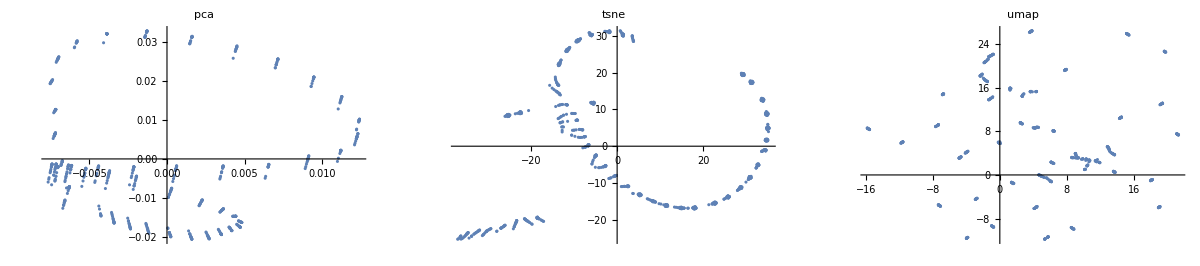

```mathematica
pca = ListPlot[{spec["y.pca"],spec["x.pca"]}//Transpose,PlotLabel->"pca"];
tsne = ListPlot[{spec["y.tsne"],spec["x.tsne"]}//Transpose, PlotLabel->"tsne"];
umap = ListPlot[{spec["y.umap"],spec["x.umap"]}//Transpose, PlotLabel->"umap"];
vis2d=GraphicsRow[{pca, tsne, umap}, ImageSize->Full]
```

```mathematica
GraphicsRow[{
FeatureSpacePlot[Transpose[{spec["x.pca"],spec["y.pca"]}]-> spec["moa"], PlotLabel->"pca"], 
FeatureSpacePlot[Transpose[{spec["x.tsne"],spec["y.tsne"]}]-> spec["moa"], PlotLabel->"tsne"],
FeatureSpacePlot[Transpose[{spec["x.umap"],spec["y.umap"]}]-> spec["moa"], PlotLabel->"umap"]}, ImageSize->Full]
```

-Graphics-